```mathematica
MyShow[m_,g_]:=TableForm[{Graph[g,GraphLayout->"TutteEmbedding",ImageSize->150, VertexLabels->"Name"],
Graph[g,GraphLayout->"CircularEmbedding",ImageSize->150, VertexLabels->"Name"],Labeled[TraditionalForm[m],Style[TraditionalForm[FullSimplify[m[[1,1]]+m[[1,2]]]],Red,Bold]]},TableDirections->Row]
```

```mathematica
MyShow2[m_,g_]:=Labeled[TableForm[m,TableHeadings->{ {1<->3,1<->4,2<->4,2<->5,3<->5,7<->3,7<->4},None}],Style[TraditionalForm[FullSimplify[m[[1,1]]+m[[1,2]]]],Red,Bold]]
```

```mathematica
ContractGraph[g_,e_]:=Graph[VertexContract[gempty,{e[[1]],e[[2]]}],VertexLabels->{e[[1]]->{e}}]
```

```mathematica
gempty:=CycleGraph[5]
```

```mathematica
empty:={{α,λ-α},{β,λ-β},{γ,λ-γ},{δ,λ-δ},{ϵ,λ-ϵ},{ζ,λ-ζ},{η,λ-η}};MyShow2[empty,gempty]
```

1<->3 | α | -α+λ
1<->4 | β | -β+λ
2<->4 | γ | -γ+λ
2<->5 | δ | -δ+λ
3<->5 | ϵ | -ϵ+λ
7<->3 | ζ | -ζ+λ
7<->4 | η | -η+λλ

```mathematica
emptywithoutonetwo = emptycontractonetwo+empty;MyShow2[emptywithoutonetwo,gempty]
```

1<->3 | emptycontractonetwo+α | emptycontractonetwo-α+λ
1<->4 | emptycontractonetwo+β | emptycontractonetwo-β+λ
2<->4 | emptycontractonetwo+γ | emptycontractonetwo-γ+λ
2<->5 | emptycontractonetwo+δ | emptycontractonetwo-δ+λ
3<->5 | emptycontractonetwo+ϵ | emptycontractonetwo-ϵ+λ
7<->3 | emptycontractonetwo+ζ | emptycontractonetwo-ζ+λ
7<->4 | emptycontractonetwo+η | emptycontractonetwo-η+λ2 emptycontractonetwo+λ

```mathematica
alfa:={{α,0},{0,α},{γ2,α-γ2},{δ1,α-δ1},{0,α},{ζ1,α-ζ1},{η1,α-η1}};MyShow2[alfa,ContractGraph[gempty,1<->3]]
```

1<->3 | α | 0
1<->4 | 0 | α
2<->4 | γ2 | α-γ2
2<->5 | δ1 | α-δ1
3<->5 | 0 | α
7<->3 | ζ1 | α-ζ1
7<->4 | η1 | α-η1α

```mathematica
alfa1:={{α1,0},{0,α1},{α1,0},{0,α1},{0,α1},{ζ6,α1-ζ6},{η6,α1-η6}};MyShow2[alfa1,Null]
```

1<->3 | α1 | 0
1<->4 | 0 | α1
2<->4 | α1 | 0
2<->5 | 0 | α1
3<->5 | 0 | α1
7<->3 | ζ6 | α1-ζ6
7<->4 | η6 | α1-η6α1

```mathematica
onethreecontract:=alfa;
```

```mathematica
onethree:=empty-alfa;MyShow2[onethree,EdgeAdd[gempty,1<->3]]
```

1<->3 | 0 | -α+λ
1<->4 | β | -α-β+λ
2<->4 | γ-γ2 | -α-γ+γ2+λ
2<->5 | δ-δ1 | -α-δ+δ1+λ
3<->5 | ϵ | -α-ϵ+λ
7<->3 | ζ-ζ1 | -α-ζ+ζ1+λ
7<->4 | η-η1 | -α-η+η1+λλ-α

```mathematica
beta:={{0,β},{β,0},{0,β},{δ2,β-δ2},{ϵ1,β-ϵ1},{ζ2,β-ζ2},{η2,β-η2}};MyShow2[beta,ContractGraph[gempty,1<->4]]
```

1<->3 | 0 | β
1<->4 | β | 0
2<->4 | 0 | β
2<->5 | δ2 | β-δ2
3<->5 | ϵ1 | β-ϵ1
7<->3 | ζ2 | β-ζ2
7<->4 | η2 | β-η2β

```mathematica
beta1:={{0,β1},{β1,0},{0,β1},{0,β1},{β1,0},{ζ7,β1-ζ7},{η7,β1-η7}};MyShow2[beta1,Null]
```

1<->3 | 0 | β1
1<->4 | β1 | 0
2<->4 | 0 | β1
2<->5 | 0 | β1
3<->5 | β1 | 0
7<->3 | ζ7 | β1-ζ7
7<->4 | η7 | β1-η7β1

```mathematica
onefourcontract:=beta;
```

```mathematica
onefour:=empty-beta;MyShow2[onefour,EdgeAdd[gempty,1<->4]]
```

1<->3 | α | -α-β+λ
1<->4 | 0 | -β+λ
2<->4 | γ | -β-γ+λ
2<->5 | δ-δ2 | -β-δ+δ2+λ
3<->5 | ϵ-ϵ1 | -β-ϵ+ϵ1+λ
7<->3 | ζ-ζ2 | -β-ζ+ζ2+λ
7<->4 | η-η2 | -β-η+η2+λλ-β

```mathematica
gamma:={{α1,γ-α1},{0,γ},{γ,0},{0,γ},{ϵ2,γ-ϵ2},{ζ3,γ-ζ3},{η3,γ-η3}};MyShow2[gamma,ContractGraph[gempty,2<->4]]
```

1<->3 | α1 | -α1+γ
1<->4 | 0 | γ
2<->4 | γ | 0
2<->5 | 0 | γ
3<->5 | ϵ2 | γ-ϵ2
7<->3 | ζ3 | γ-ζ3
7<->4 | η3 | γ-η3γ

```mathematica
gamma1:={{0,γ1},{0,γ1},{0,γ1} ,{γ1,0},{γ1,0} ,{ζ8,γ1-ζ8},{η8,γ1-η8}};MyShow2[gamma1,Null]
```

1<->3 | 0 | γ1
1<->4 | 0 | γ1
2<->4 | 0 | γ1
2<->5 | γ1 | 0
3<->5 | γ1 | 0
7<->3 | ζ8 | γ1-ζ8
7<->4 | η8 | γ1-η8γ1

```mathematica
twofourcontract:=gamma;
```

```mathematica
twofour:=empty-gamma;MyShow2[twofour,EdgeAdd[gempty,2<->4]]
```

1<->3 | α-α1 | -α+α1-γ+λ
1<->4 | β | -β-γ+λ
2<->4 | 0 | -γ+λ
2<->5 | δ | -γ-δ+λ
3<->5 | ϵ-ϵ2 | -γ-ϵ+ϵ2+λ
7<->3 | ζ-ζ3 | -γ-ζ+ζ3+λ
7<->4 | η-η3 | -γ-η+η3+λλ-γ

```mathematica
delta:={{α2,δ-α2},{β1,δ-β1},{0,δ},{δ,0},{0,δ},{ζ4,δ-ζ4},{η4,δ-η4}};MyShow2[delta,ContractGraph[gempty,2<->5]]
```

1<->3 | α2 | -α2+δ
1<->4 | β1 | -β1+δ
2<->4 | 0 | δ
2<->5 | δ | 0
3<->5 | 0 | δ
7<->3 | ζ4 | δ-ζ4
7<->4 | η4 | δ-η4δ

```mathematica
delta1:={{δ1,0},{0,δ1},{0,δ1},{δ1,0},{0,δ1},{ζ9,δ1-ζ9},{η9,δ1-η9}};MyShow2[delta1,Null]
```

1<->3 | δ1 | 0
1<->4 | 0 | δ1
2<->4 | 0 | δ1
2<->5 | δ1 | 0
3<->5 | 0 | δ1
7<->3 | ζ7 | δ1-ζ7
7<->4 | η7 | δ1-η7δ1

```mathematica
twofivecontract:=delta;
```

```mathematica
twofive:=empty-delta;MyShow2[twofive,EdgeAdd[gempty,2<->5]]
```

1<->3 | α-α2 | -α+α2-δ+λ
1<->4 | β-β1 | -β+β1-δ+λ
2<->4 | γ | -γ-δ+λ
2<->5 | 0 | -δ+λ
3<->5 | ϵ | -δ-ϵ+λ
7<->3 | ζ-ζ4 | -δ-ζ+ζ4+λ
7<->4 | η-η4 | -δ-η+η4+λλ-δ

```mathematica
epsilon:={{0,ϵ},{β2,ϵ-β2},{γ1,ϵ-γ1},{0,ϵ},{ϵ,0},{ζ5,ϵ-ζ5},{η5,ϵ-η5}};MyShow2[epsilon,ContractGraph[gempty,3<->5]]
```

1<->3 | 0 | ϵ
1<->4 | β2 | -β2+ϵ
2<->4 | γ1 | -γ1+ϵ
2<->5 | 0 | ϵ
3<->5 | ϵ | 0
7<->3 | ζ5 | ϵ-ζ5
7<->4 | η5 | ϵ-η5ϵ

```mathematica
epsilon1:={{0,ϵ1},{ϵ1,0},{0,ϵ1},{0,ϵ1},{ϵ1,0},{ζ10,ϵ1-ζ10},{η10,ϵ1-η10}};MyShow2[epsilon1,Null]
```

1<->3 | 0 | ϵ1
1<->4 | ϵ1 | 0
2<->4 | 0 | ϵ1
2<->5 | 0 | ϵ1
3<->5 | ϵ1 | 0
7<->3 | ζ10 | ϵ1-ζ10
7<->4 | η10 | ϵ1-η10ϵ1

```mathematica
threefive:=empty-epsilon;MyShow2[threefive,EdgeAdd[gempty,3<->5]]
```

1<->3 | α | -α-ϵ+λ
1<->4 | β-β2 | -β+β2-ϵ+λ
2<->4 | γ-γ1 | -γ+γ1-ϵ+λ
2<->5 | δ | -δ-ϵ+λ
3<->5 | 0 | -ϵ+λ
7<->3 | ζ-ζ5 | -ϵ-ζ+ζ5+λ
7<->4 | η-η5 | -ϵ-η+η5+λλ-ϵ

```mathematica
threefivecontract:=epsilon;
```

```mathematica
oneamigo1:=onethree-onefourcontract;MyShow2[oneamigo1,EdgeAdd[gempty,{1<->3,1<->4}]]
```

1<->3 | 0 | -α-β+λ
1<->4 | 0 | -α-β+λ
2<->4 | γ-γ2 | -α-β-γ+γ2+λ
2<->5 | δ-δ1-δ2 | -α-β-δ+δ1+δ2+λ
3<->5 | ϵ-ϵ1 | -α-β-ϵ+ϵ1+λ
7<->3 | ζ-ζ1-ζ2 | -α-β-ζ+ζ1+ζ2+λ
7<->4 | η-η1-η2 | -α-β-η+η1+η2+λ-α-β+λ

```mathematica
oneamigo2:=twofive-twofourcontract;MyShow2[oneamigo2,EdgeAdd[gempty,{2<->5,2<->4}]]
```

1<->3 | α-α1-α2 | -α+α1+α2-γ-δ+λ
1<->4 | β-β1 | -β+β1-γ-δ+λ
2<->4 | 0 | -γ-δ+λ
2<->5 | 0 | -γ-δ+λ
3<->5 | ϵ-ϵ2 | -γ-δ-ϵ+ϵ2+λ
7<->3 | ζ-ζ3-ζ4 | -γ-δ-ζ+ζ3+ζ4+λ
7<->4 | η-η3-η4 | -γ-δ-η+η3+η4+λ-γ-δ+λ

```mathematica
oneamigo3:=threefive;
```

```mathematica
twoamigo1:=twofive-twofourcontract;MyShow2[twoamigo1,EdgeAdd[gempty,{2<->5,2<->4}]]
```

1<->3 | α-α1-α2 | -α+α1+α2-γ-δ+λ
1<->4 | β-β1 | -β+β1-γ-δ+λ
2<->4 | 0 | -γ-δ+λ
2<->5 | 0 | -γ-δ+λ
3<->5 | ϵ-ϵ2 | -γ-δ-ϵ+ϵ2+λ
7<->3 | ζ-ζ3-ζ4 | -γ-δ-ζ+ζ3+ζ4+λ
7<->4 | η-η3-η4 | -γ-δ-η+η3+η4+λ-γ-δ+λ

```mathematica
twoamigo2:=onethree-threefivecontract;MyShow2[twoamigo2,EdgeAdd[gempty,{3<->5,3<->1}]]
```

1<->3 | 0 | -α-ϵ+λ
1<->4 | β-β2 | -α-β+β2-ϵ+λ
2<->4 | γ-γ1-γ2 | -α-γ+γ1+γ2-ϵ+λ
2<->5 | δ-δ1 | -α-δ+δ1-ϵ+λ
3<->5 | 0 | -α-ϵ+λ
7<->3 | ζ-ζ1-ζ5 | -α-ϵ-ζ+ζ1+ζ5+λ
7<->4 | η-η1-η5 | -α-ϵ-η+η1+η5+λ-α+λ-ϵ

```mathematica
twoamigo3:=onefour;
```

```mathematica
threeamigo1:=onethree-threefivecontract;MyShow2[threeamigo1,EdgeAdd[gempty,{3<->5,3<->1}]]
```

1<->3 | 0 | -α-ϵ+λ
1<->4 | β-β2 | -α-β+β2-ϵ+λ
2<->4 | γ-γ1-γ2 | -α-γ+γ1+γ2-ϵ+λ
2<->5 | δ-δ1 | -α-δ+δ1-ϵ+λ
3<->5 | 0 | -α-ϵ+λ
7<->3 | ζ-ζ1-ζ5 | -α-ϵ-ζ+ζ1+ζ5+λ
7<->4 | η-η1-η5 | -α-ϵ-η+η1+η5+λ-α+λ-ϵ

```mathematica
threeamigo2:=onefour-twofourcontract;MyShow2[threeamigo2,EdgeAdd[gempty,{4<->1,4<->2}]]
```

1<->3 | α-α1 | -α+α1-β-γ+λ
1<->4 | 0 | -β-γ+λ
2<->4 | 0 | -β-γ+λ
2<->5 | δ-δ2 | -β-γ-δ+δ2+λ
3<->5 | ϵ-ϵ1-ϵ2 | -β-γ-ϵ+ϵ1+ϵ2+λ
7<->3 | ζ-ζ2-ζ3 | -β-γ-ζ+ζ2+ζ3+λ
7<->4 | η-η2-η3 | -β-γ-η+η2+η3+λ-β-γ+λ

```mathematica
threeamigo3:=twofive;
```

```mathematica
fouramigo1:=onefour-twofourcontract;MyShow2[fouramigo1,EdgeAdd[gempty,{4<->1,4<->2}]]
```

1<->3 | α-α1 | -α+α1-β-γ+λ
1<->4 | 0 | -β-γ+λ
2<->4 | 0 | -β-γ+λ
2<->5 | δ-δ2 | -β-γ-δ+δ2+λ
3<->5 | ϵ-ϵ1-ϵ2 | -β-γ-ϵ+ϵ1+ϵ2+λ
7<->3 | ζ-ζ2-ζ3 | -β-γ-ζ+ζ2+ζ3+λ
7<->4 | η-η2-η3 | -β-γ-η+η2+η3+λ-β-γ+λ

```mathematica
fouramigo2:=twofive-threefivecontract;MyShow2[fouramigo2,EdgeAdd[gempty,{5<->2,5<->3}]]
```

1<->3 | α-α2 | -α+α2-δ-ϵ+λ
1<->4 | β-β1-β2 | -β+β1+β2-δ-ϵ+λ
2<->4 | γ-γ1 | -γ+γ1-δ-ϵ+λ
2<->5 | 0 | -δ-ϵ+λ
3<->5 | 0 | -δ-ϵ+λ
7<->3 | ζ-ζ4-ζ5 | -δ-ϵ-ζ+ζ4+ζ5+λ
7<->4 | η-η4-η5 | -δ-ϵ-η+η4+η5+λ-δ+λ-ϵ

```mathematica
fouramigo3:=onethree;
```

```mathematica
fiveamigo1:=twofive-threefivecontract;MyShow2[fiveamigo1,EdgeAdd[gempty,{5<->2,5<->3}]]
```

1<->3 | α-α2 | -α+α2-δ-ϵ+λ
1<->4 | β-β1-β2 | -β+β1+β2-δ-ϵ+λ
2<->4 | γ-γ1 | -γ+γ1-δ-ϵ+λ
2<->5 | 0 | -δ-ϵ+λ
3<->5 | 0 | -δ-ϵ+λ
7<->3 | ζ-ζ4-ζ5 | -δ-ϵ-ζ+ζ4+ζ5+λ
7<->4 | η-η4-η5 | -δ-ϵ-η+η4+η5+λ-δ+λ-ϵ

```mathematica
fiveamigo2:=onethree-onefourcontract;MyShow2[fiveamigo2,EdgeAdd[gempty,{1<->3,1<->4}]]
```

1<->3 | 0 | -α-β+λ
1<->4 | 0 | -α-β+λ
2<->4 | γ-γ2 | -α-β-γ+γ2+λ
2<->5 | δ-δ1-δ2 | -α-β-δ+δ1+δ2+λ
3<->5 | ϵ-ϵ1 | -α-β-ϵ+ϵ1+λ
7<->3 | ζ-ζ1-ζ2 | -α-β-ζ+ζ1+ζ2+λ
7<->4 | η-η1-η2 | -α-β-η+η1+η2+λ-α-β+λ

```mathematica
fiveamigo3:=twofour;
```

```mathematica
full:=2*empty-( oneamigo1+oneamigo2+oneamigo3)//FullSimplify;MyShow2[full,EdgeAdd[gempty,Table[i<->6,{i,5}]]]
```

1<->3 | α1+α2 | α-α1-α2+β+γ+δ+ϵ-λ
1<->4 | β1+β2 | α+β-β1-β2+γ+δ+ϵ-λ
2<->4 | γ1+γ2 | α+β+γ-γ1-γ2+δ+ϵ-λ
2<->5 | δ1+δ2 | α+β+γ+δ-δ1-δ2+ϵ-λ
3<->5 | ϵ1+ϵ2 | α+β+γ+δ+ϵ-ϵ1-ϵ2-λ
7<->3 | -ζ+ζ1+ζ2+ζ3+ζ4+ζ5 | α+β+γ+δ+ϵ+ζ-ζ1-ζ2-ζ3-ζ4-ζ5-λ
7<->4 | -η+η1+η2+η3+η4+η5 | α+β+γ+δ+ϵ+η-η1-η2-η3-η4-η5-λα+β+γ+δ-λ+ϵ

```mathematica
onegone:=full+oneamigo1//FullSimplify;MyShow2[onegone,EdgeAdd[gempty,Table[i<->6,{i,{2,3,4,5}}]]]
```

1<->3 | α1+α2 | -α1-α2+γ+δ+ϵ
1<->4 | β1+β2 | -β1-β2+γ+δ+ϵ
2<->4 | γ+γ1 | -γ1+δ+ϵ
2<->5 | δ | γ+ϵ
3<->5 | ϵ+ϵ2 | γ+δ-ϵ2
7<->3 | ζ3+ζ4+ζ5 | γ+δ+ϵ-ζ3-ζ4-ζ5
7<->4 | η3+η4+η5 | γ+δ+ϵ-η3-η4-η5γ+δ+ϵ

```mathematica
fivegone:=full+fiveamigo1//FullSimplify;MyShow2[fivegone,EdgeAdd[gempty,Table[i<->6,{i,{1,2,3,4}}]]]
```

1<->3 | α+α1 | -α1+β+γ
1<->4 | β | α+γ
2<->4 | γ+γ2 | α+β-γ2
2<->5 | δ1+δ2 | α+β+γ-δ1-δ2
3<->5 | ϵ1+ϵ2 | α+β+γ-ϵ1-ϵ2
7<->3 | ζ1+ζ2+ζ3 | α+β+γ-ζ1-ζ2-ζ3
7<->4 | η1+η2+η3 | α+β+γ-η1-η2-η3α+β+γ

```mathematica
twogone:=full+twoamigo1//FullSimplify;MyShow2[twogone,EdgeAdd[gempty,Table[i<->6,{i,{1,3,4,5}}]]]
```

1<->3 | α | β+ϵ
1<->4 | β+β2 | α-β2+ϵ
2<->4 | γ1+γ2 | α+β-γ1-γ2+ϵ
2<->5 | δ1+δ2 | α+β-δ1-δ2+ϵ
3<->5 | ϵ+ϵ1 | α+β-ϵ1
7<->3 | ζ1+ζ2+ζ5 | α+β+ϵ-ζ1-ζ2-ζ5
7<->4 | η1+η2+η5 | α+β+ϵ-η1-η2-η5α+β+ϵ

```mathematica
onefivegone:=full+fiveamigo1+oneamigo1//FullSimplify;MyShow2[onefivegone,EdgeAdd[gempty,Table[i<->6,{i,{2,3,4}}]]]
```

1<->3 | α+α1 | -α-α1+γ+λ
1<->4 | β | -β+γ+λ
2<->4 | 2 γ | -γ+λ
2<->5 | δ | γ-δ+λ
3<->5 | ϵ+ϵ2 | γ-ϵ-ϵ2+λ
7<->3 | ζ+ζ3 | γ-ζ-ζ3+λ
7<->4 | η+η3 | γ-η-η3+λγ+λ

```mathematica
onetwofivegone:=onefivegone+delta//FullSimplify;MyShow2[onetwofivegone,EdgeAdd[gempty,Table[i<->6,{i,{3,4}}]]]
```

1<->3 | α+α1+α2 | -α-α1-α2+γ+δ+λ
1<->4 | β+β1 | -β-β1+γ+δ+λ
2<->4 | 2 γ | -γ+δ+λ
2<->5 | 2 δ | γ-δ+λ
3<->5 | ϵ+ϵ2 | γ+δ-ϵ-ϵ2+λ
7<->3 | ζ+ζ3+ζ4 | γ+δ-ζ-ζ3-ζ4+λ
7<->4 | η+η3+η4 | γ+δ-η-η3-η4+λγ+δ+λ

```mathematica
onethreefivegone:=onefivegone+delta//FullSimplify;MyShow2[onetwofivegone,EdgeAdd[gempty,Table[i<->6,{i,{3,4}}]]]
```

1<->3 | α+α1+α2 | -α-α1-α2+γ+δ+λ
1<->4 | β+β1 | -β-β1+γ+δ+λ
2<->4 | 2 γ | -γ+δ+λ
2<->5 | 2 δ | γ-δ+λ
3<->5 | ϵ+ϵ2 | γ+δ-ϵ-ϵ2+λ
7<->3 | ζ+ζ3+ζ4 | γ+δ-ζ-ζ3-ζ4+λ
7<->4 | η+η3+η4 | γ+δ-η-η3-η4+λγ+δ+λ

```mathematica
withoutspike1:=full+oneamigo1//FullSimplify;MyShow2[withoutspike1,EdgeAdd[gempty,Table[i<->6,{i,2,5}]]]
```

1<->3 | α1+α2 | -α1-α2+γ+δ+ϵ
1<->4 | β1+β2 | -β1-β2+γ+δ+ϵ
2<->4 | γ+γ1 | -γ1+δ+ϵ
2<->5 | δ | γ+ϵ
3<->5 | ϵ+ϵ2 | γ+δ-ϵ2
7<->3 | ζ3+ζ4+ζ5 | γ+δ+ϵ-ζ3-ζ4-ζ5
7<->4 | η3+η4+η5 | γ+δ+ϵ-η3-η4-η5γ+δ+ϵ

```mathematica
withoutspike2:=full+oneamigo2//FullSimplify;MyShow2[withoutspike2,EdgeAdd[gempty,Table[i<->6,{i,{1,3,4,5}}]]]
```

1<->3 | α | β+ϵ
1<->4 | β+β2 | α-β2+ϵ
2<->4 | γ1+γ2 | α+β-γ1-γ2+ϵ
2<->5 | δ1+δ2 | α+β-δ1-δ2+ϵ
3<->5 | ϵ+ϵ1 | α+β-ϵ1
7<->3 | ζ1+ζ2+ζ5 | α+β+ϵ-ζ1-ζ2-ζ5
7<->4 | η1+η2+η5 | α+β+ϵ-η1-η2-η5α+β+ϵ

```mathematica
without2spikes1:=withoutspike1+oneamigo2//FullSimplify;MyShow2[without2spikes1,EdgeAdd[gempty,Table[i<->6,{i,{3,4,5}}]]]
```

1<->3 | α | -α+ϵ+λ
1<->4 | β+β2 | -β-β2+ϵ+λ
2<->4 | γ+γ1 | -γ-γ1+ϵ+λ
2<->5 | δ | -δ+ϵ+λ
3<->5 | 2 ϵ | -ϵ+λ
7<->3 | ζ+ζ5 | ϵ-ζ-ζ5+λ
7<->4 | η+η5 | ϵ-η-η5+λλ+ϵ

```mathematica
without3spikes1:=without2spikes1+empty//FullSimplify;MyShow2[without3spikes1,EdgeAdd[gempty,Table[i<->6,{i,{1,5}}]]]
```

1<->3 | 2 α | -2 α+ϵ+2 λ
1<->4 | 2 β+β2 | -2 β-β2+ϵ+2 λ
2<->4 | 2 γ+γ1 | -2 γ-γ1+ϵ+2 λ
2<->5 | 2 δ | -2 δ+ϵ+2 λ
3<->5 | 3 ϵ | -2 ϵ+2 λ
7<->3 | 2 ζ+ζ5 | ϵ-2 ζ-ζ5+2 λ
7<->4 | 2 η+η5 | ϵ-2 η-η5+2 λ2 λ+ϵ

```mathematica
without2spikes2:=withoutspike2+oneamigo1//FullSimplify;MyShow2[without2spikes2,EdgeAdd[gempty,Table[i<->6,{i,{3,4,5}}]]]
```

1<->3 | α | -α+ϵ+λ
1<->4 | β+β2 | -β-β2+ϵ+λ
2<->4 | γ+γ1 | -γ-γ1+ϵ+λ
2<->5 | δ | -δ+ϵ+λ
3<->5 | 2 ϵ | -ϵ+λ
7<->3 | ζ+ζ5 | ϵ-ζ-ζ5+λ
7<->4 | η+η5 | ϵ-η-η5+λλ+ϵ

```mathematica
without3spikes2:=without2spikes2+empty//FullSimplify;MyShow2[without3spikes2,EdgeAdd[gempty,Table[i<->6,{i,{1,5}}]]]
```

1<->3 | 2 α | -2 α+ϵ+2 λ
1<->4 | 2 β+β2 | -2 β-β2+ϵ+2 λ
2<->4 | 2 γ+γ1 | -2 γ-γ1+ϵ+2 λ
2<->5 | 2 δ | -2 δ+ϵ+2 λ
3<->5 | 3 ϵ | -2 ϵ+2 λ
7<->3 | 2 ζ+ζ5 | ϵ-2 ζ-ζ5+2 λ
7<->4 | 2 η+η5 | ϵ-2 η-η5+2 λ2 λ+ϵ

```mathematica
Assuming[
{α>0,β>0,γ>0,δ>0,ϵ>0,α1>=0,α2>=0,β1>=0,β2>=0,γ1>=0,γ2>=0,δ1>=0,δ2>=0,ϵ1>=0,ϵ>=0},
Solve[2*empty-( oneamigo1+oneamigo2+oneamigo3)=={{0,0},{0,0},{0,0},{0,0},{0,0}}]
]
```

{}

```mathematica
Clear[sols]
```

```mathematica
sols=Association[]
```

<||>

```mathematica
sols[1]=empty
```

{{α,-α+λ},{β,-β+λ},{γ,-γ+λ},{δ,-δ+λ},{ϵ,-ϵ+λ},{ζ,-ζ+λ},{η,-η+λ}}

```mathematica
sols[2]=alfa
```

{{α,0},{0,α},{γ2,α-γ2},{δ1,α-δ1},{0,α},{ζ1,α-ζ1},{η1,α-η1}}

```mathematica
sols[3]=sols[1]-sols[2]
```

{{0,-α+λ},{β,-α-β+λ},{γ-γ2,-α-γ+γ2+λ},{δ-δ1,-α-δ+δ1+λ},{ϵ,-α-ϵ+λ},{ζ-ζ1,-α-ζ+ζ1+λ},{η-η1,-α-η+η1+λ}}

```mathematica
sols[4]=beta
```

{{0,β},{β,0},{0,β},{δ2,β-δ2},{ϵ1,β-ϵ1},{ζ2,β-ζ2},{η2,β-η2}}

```mathematica
sols[5]=sols[1]-sols[4]
```

{{α,-α-β+λ},{0,-β+λ},{γ,-β-γ+λ},{δ-δ2,-β-δ+δ2+λ},{ϵ-ϵ1,-β-ϵ+ϵ1+λ},{ζ-ζ2,-β-ζ+ζ2+λ},{η-η2,-β-η+η2+λ}}

```mathematica
sols[6]=gamma
```

{{α1,-α1+γ},{0,γ},{γ,0},{0,γ},{ϵ2,γ-ϵ2},{ζ3,γ-ζ3},{η3,γ-η3}}

```mathematica
sols[7]=sols[1]-sols[6]
```

{{α-α1,-α+α1-γ+λ},{β,-β-γ+λ},{0,-γ+λ},{δ,-γ-δ+λ},{ϵ-ϵ2,-γ-ϵ+ϵ2+λ},{ζ-ζ3,-γ-ζ+ζ3+λ},{η-η3,-γ-η+η3+λ}}

```mathematica
sols[8]=delta
```

{{α2,-α2+δ},{β1,-β1+δ},{0,δ},{δ,0},{0,δ},{ζ4,δ-ζ4},{η4,δ-η4}}

```mathematica
sols[9]=sols[1]-sols[8]
```

{{α-α2,-α+α2-δ+λ},{β-β1,-β+β1-δ+λ},{γ,-γ-δ+λ},{0,-δ+λ},{ϵ,-δ-ϵ+λ},{ζ-ζ4,-δ-ζ+ζ4+λ},{η-η4,-δ-η+η4+λ}}

```mathematica
sols[10]=epsilon
```

{{0,ϵ},{β2,-β2+ϵ},{γ1,-γ1+ϵ},{0,ϵ},{ϵ,0},{ζ5,ϵ-ζ5},{η5,ϵ-η5}}

```mathematica
sols[11]=sols[1]-sols[10]
```

{{α,-α-ϵ+λ},{β-β2,-β+β2-ϵ+λ},{γ-γ1,-γ+γ1-ϵ+λ},{δ,-δ-ϵ+λ},{0,-ϵ+λ},{ζ-ζ5,-ϵ-ζ+ζ5+λ},{η-η5,-ϵ-η+η5+λ}}

```mathematica
sols[12]=sols[5]-sols[2]
```

{{0,-α-β+λ},{0,-α-β+λ},{γ-γ2,-α-β-γ+γ2+λ},{δ-δ1-δ2,-α-β-δ+δ1+δ2+λ},{ϵ-ϵ1,-α-β-ϵ+ϵ1+λ},{ζ-ζ1-ζ2,-α-β-ζ+ζ1+ζ2+λ},{η-η1-η2,-α-β-η+η1+η2+λ}}

```mathematica
sols[13]=sols[9]-sols[6]
```

{{α-α1-α2,-α+α1+α2-γ-δ+λ},{β-β1,-β+β1-γ-δ+λ},{0,-γ-δ+λ},{0,-γ-δ+λ},{ϵ-ϵ2,-γ-δ-ϵ+ϵ2+λ},{ζ-ζ3-ζ4,-γ-δ-ζ+ζ3+ζ4+λ},{η-η3-η4,-γ-δ-η+η3+η4+λ}}

```mathematica
sols[14]=sols[3]-sols[10]
```

{{0,-α-ϵ+λ},{β-β2,-α-β+β2-ϵ+λ},{γ-γ1-γ2,-α-γ+γ1+γ2-ϵ+λ},{δ-δ1,-α-δ+δ1-ϵ+λ},{0,-α-ϵ+λ},{ζ-ζ1-ζ5,-α-ϵ-ζ+ζ1+ζ5+λ},{η-η1-η5,-α-ϵ-η+η1+η5+λ}}

```mathematica
sols[15]=sols[5]-sols[6]
```

{{α-α1,-α+α1-β-γ+λ},{0,-β-γ+λ},{0,-β-γ+λ},{δ-δ2,-β-γ-δ+δ2+λ},{ϵ-ϵ1-ϵ2,-β-γ-ϵ+ϵ1+ϵ2+λ},{ζ-ζ2-ζ3,-β-γ-ζ+ζ2+ζ3+λ},{η-η2-η3,-β-γ-η+η2+η3+λ}}

```mathematica
sols[16]=sols[9]-sols[10]
```

{{α-α2,-α+α2-δ-ϵ+λ},{β-β1-β2,-β+β1+β2-δ-ϵ+λ},{γ-γ1,-γ+γ1-δ-ϵ+λ},{0,-δ-ϵ+λ},{0,-δ-ϵ+λ},{ζ-ζ4-ζ5,-δ-ϵ-ζ+ζ4+ζ5+λ},{η-η4-η5,-δ-ϵ-η+η4+η5+λ}}

```mathematica
sols[17]=2sols[1]-(sols[12]+sols[13]+sols[11])//FullSimplify
```

{{α1+α2,α-α1-α2+β+γ+δ+ϵ-λ},{β1+β2,α+β-β1-β2+γ+δ+ϵ-λ},{γ1+γ2,α+β+γ-γ1-γ2+δ+ϵ-λ},{δ1+δ2,α+β+γ+δ-δ1-δ2+ϵ-λ},{ϵ1+ϵ2,α+β+γ+δ+ϵ-ϵ1-ϵ2-λ},{-ζ+ζ1+ζ2+ζ3+ζ4+ζ5,α+β+γ+δ+ϵ+ζ-ζ1-ζ2-ζ3-ζ4-ζ5-λ},{-η+η1+η2+η3+η4+η5,α+β+γ+δ+ϵ+η-η1-η2-η3-η4-η5-λ}}

```mathematica
sols[18]=sols[12]+sols[17]
```

{{α1+α2,-α1-α2+γ+δ+ϵ},{β1+β2,-β1-β2+γ+δ+ϵ},{γ+γ1,-γ1+δ+ϵ},{δ,γ+ϵ},{ϵ+ϵ2,γ+δ-ϵ2},{ζ3+ζ4+ζ5,γ+δ+ϵ-ζ3-ζ4-ζ5},{η3+η4+η5,γ+δ+ϵ-η3-η4-η5}}

```mathematica
sols[19]=sols[13]+sols[17]
```

{{α,β+ϵ},{β+β2,α-β2+ϵ},{γ1+γ2,α+β-γ1-γ2+ϵ},{δ1+δ2,α+β-δ1-δ2+ϵ},{ϵ+ϵ1,α+β-ϵ1},{ζ1+ζ2+ζ5,α+β+ϵ-ζ1-ζ2-ζ5},{η1+η2+η5,α+β+ϵ-η1-η2-η5}}

```mathematica
sols[20]=sols[14]+sols[17]
```

{{α1+α2,-α1-α2+β+γ+δ},{β+β1,-β1+γ+δ},{γ,β+δ},{δ+δ2,β+γ-δ2},{ϵ1+ϵ2,β+γ+δ-ϵ1-ϵ2},{ζ2+ζ3+ζ4,β+γ+δ-ζ2-ζ3-ζ4},{η2+η3+η4,β+γ+δ-η2-η3-η4}}

```mathematica
sols[21]=sols[15]+sols[17]
```

{{α+α2,-α2+δ+ϵ},{β1+β2,α-β1-β2+δ+ϵ},{γ1+γ2,α-γ1-γ2+δ+ϵ},{δ+δ1,α-δ1+ϵ},{ϵ,α+δ},{ζ1+ζ4+ζ5,α+δ+ϵ-ζ1-ζ4-ζ5},{η1+η4+η5,α+δ+ϵ-η1-η4-η5}}

```mathematica
sols[22]=sols[16]+sols[17]
```

{{α+α1,-α1+β+γ},{β,α+γ},{γ+γ2,α+β-γ2},{δ1+δ2,α+β+γ-δ1-δ2},{ϵ1+ϵ2,α+β+γ-ϵ1-ϵ2},{ζ1+ζ2+ζ3,α+β+γ-ζ1-ζ2-ζ3},{η1+η2+η3,α+β+γ-η1-η2-η3}}

```mathematica
sols[23]=sols[18]+sols[13]
```

{{α,-α+ϵ+λ},{β+β2,-β-β2+ϵ+λ},{γ+γ1,-γ-γ1+ϵ+λ},{δ,-δ+ϵ+λ},{2 ϵ,-ϵ+λ},{ζ+ζ5,ϵ-ζ-ζ5+λ},{η+η5,ϵ-η-η5+λ}}

```mathematica
sols[24]=sols[19]+sols[14]
```

{{α,-α+β+λ},{2 β,-β+λ},{γ,β-γ+λ},{δ+δ2,β-δ-δ2+λ},{ϵ+ϵ1,β-ϵ-ϵ1+λ},{ζ+ζ2,β-ζ-ζ2+λ},{η+η2,β-η-η2+λ}}

```mathematica
sols[25]=sols[20]+sols[15]
```

{{α+α2,-α-α2+δ+λ},{β+β1,-β-β1+δ+λ},{γ,-γ+δ+λ},{2 δ,-δ+λ},{ϵ,δ-ϵ+λ},{ζ+ζ4,δ-ζ-ζ4+λ},{η+η4,δ-η-η4+λ}}

```mathematica
sols[26]=sols[21]+sols[16]
```

{{2 α,-α+λ},{β,α-β+λ},{γ+γ2,α-γ-γ2+λ},{δ+δ1,α-δ-δ1+λ},{ϵ,α-ϵ+λ},{ζ+ζ1,α-ζ-ζ1+λ},{η+η1,α-η-η1+λ}}

```mathematica
sols[27]=sols[22]+sols[12]//FullSimplify
```

{{α+α1,-α-α1+γ+λ},{β,-β+γ+λ},{2 γ,-γ+λ},{δ,γ-δ+λ},{ϵ+ϵ2,γ-ϵ-ϵ2+λ},{ζ+ζ3,γ-ζ-ζ3+λ},{η+η3,γ-η-η3+λ}}

```mathematica
sols[28]=sols[23]+sols[11]//FullSimplify
```

{{2 α,-2 α+2 λ},{2 β,-2 β+2 λ},{2 γ,-2 γ+2 λ},{2 δ,-2 δ+2 λ},{2 ϵ,-2 ϵ+2 λ},{2 ζ,-2 ζ+2 λ},{2 η,-2 η+2 λ}}

```mathematica
sols[29]=sols[24]+sols[5]//FullSimplify
```

{{2 α,-2 α+2 λ},{2 β,-2 β+2 λ},{2 γ,-2 γ+2 λ},{2 δ,-2 δ+2 λ},{2 ϵ,-2 ϵ+2 λ},{2 ζ,-2 ζ+2 λ},{2 η,-2 η+2 λ}}

```mathematica
sols[30]=sols[25]+sols[9]//FullSimplify
```

{{2 α,-2 α+2 λ},{2 β,-2 β+2 λ},{2 γ,-2 γ+2 λ},{2 δ,-2 δ+2 λ},{2 ϵ,-2 ϵ+2 λ},{2 ζ,-2 ζ+2 λ},{2 η,-2 η+2 λ}}

```mathematica
sols[31]=sols[26]+sols[3]//FullSimplify
```

{{2 α,-2 α+2 λ},{2 β,-2 β+2 λ},{2 γ,-2 γ+2 λ},{2 δ,-2 δ+2 λ},{2 ϵ,-2 ϵ+2 λ},{2 ζ,-2 ζ+2 λ},{2 η,-2 η+2 λ}}

```mathematica
sols[32]=sols[27]+sols[7]//FullSimplify
```

{{2 α,-2 α+2 λ},{2 β,-2 β+2 λ},{2 γ,-2 γ+2 λ},{2 δ,-2 δ+2 λ},{2 ϵ,-2 ϵ+2 λ},{2 ζ,-2 ζ+2 λ},{2 η,-2 η+2 λ}}

```mathematica
sols[33]=sols[23]+sols[1]//FullSimplify
```

{{2 α,-2 α+ϵ+2 λ},{2 β+β2,-2 β-β2+ϵ+2 λ},{2 γ+γ1,-2 γ-γ1+ϵ+2 λ},{2 δ,-2 δ+ϵ+2 λ},{3 ϵ,-2 ϵ+2 λ},{2 ζ+ζ5,ϵ-2 ζ-ζ5+2 λ},{2 η+η5,ϵ-2 η-η5+2 λ}}

```mathematica
sols[34]=sols[24]+sols[1]//FullSimplify
```

{{2 α,-2 α+β+2 λ},{3 β,-2 β+2 λ},{2 γ,β-2 γ+2 λ},{2 δ+δ2,β-2 δ-δ2+2 λ},{2 ϵ+ϵ1,β-2 ϵ-ϵ1+2 λ},{2 ζ+ζ2,β-2 ζ-ζ2+2 λ},{2 η+η2,β-2 η-η2+2 λ}}

```mathematica
sols[35]=sols[25]+sols[1]//FullSimplify
```

{{2 α+α2,-2 α-α2+δ+2 λ},{2 β+β1,-2 β-β1+δ+2 λ},{2 γ,-2 γ+δ+2 λ},{3 δ,-2 δ+2 λ},{2 ϵ,δ-2 ϵ+2 λ},{2 ζ+ζ4,δ-2 ζ-ζ4+2 λ},{2 η+η4,δ-2 η-η4+2 λ}}

```mathematica
sols[36]=sols[26]+sols[1]//FullSimplify
```

{{3 α,-2 α+2 λ},{2 β,α-2 β+2 λ},{2 γ+γ2,α-2 γ-γ2+2 λ},{2 δ+δ1,α-2 δ-δ1+2 λ},{2 ϵ,α-2 ϵ+2 λ},{2 ζ+ζ1,α-2 ζ-ζ1+2 λ},{2 η+η1,α-2 η-η1+2 λ}}

```mathematica
sols[37]=sols[27]+sols[1]//FullSimplify
```

{{2 α+α1,-2 α-α1+γ+2 λ},{2 β,-2 β+γ+2 λ},{3 γ,-2 γ+2 λ},{2 δ,γ-2 δ+2 λ},{2 ϵ+ϵ2,γ-2 ϵ-ϵ2+2 λ},{2 ζ+ζ3,γ-2 ζ-ζ3+2 λ},{2 η+η3,γ-2 η-η3+2 λ}}

```mathematica
sols[38]=sols[33]+sols[11]//FullSimplify
```

{{3 α,-3 α+3 λ},{3 β,-3 β+3 λ},{3 γ,-3 γ+3 λ},{3 δ,-3 δ+3 λ},{3 ϵ,-3 ϵ+3 λ},{3 ζ,-3 ζ+3 λ},{3 η,-3 η+3 λ}}

```mathematica
sols[39]=sols[34]+sols[5]//FullSimplify
```

{{3 α,-3 α+3 λ},{3 β,-3 β+3 λ},{3 γ,-3 γ+3 λ},{3 δ,-3 δ+3 λ},{3 ϵ,-3 ϵ+3 λ},{3 ζ,-3 ζ+3 λ},{3 η,-3 η+3 λ}}

```mathematica
sols[40]=sols[35]+sols[9]//FullSimplify
```

{{3 α,-3 α+3 λ},{3 β,-3 β+3 λ},{3 γ,-3 γ+3 λ},{3 δ,-3 δ+3 λ},{3 ϵ,-3 ϵ+3 λ},{3 ζ,-3 ζ+3 λ},{3 η,-3 η+3 λ}}

```mathematica
sols[41]=sols[36]+sols[3]//FullSimplify
```

{{3 α,-3 α+3 λ},{3 β,-3 β+3 λ},{3 γ,-3 γ+3 λ},{3 δ,-3 δ+3 λ},{3 ϵ,-3 ϵ+3 λ},{3 ζ,-3 ζ+3 λ},{3 η,-3 η+3 λ}}

```mathematica
sols[42]=sols[37]+sols[7]//FullSimplify
```

{{3 α,-3 α+3 λ},{3 β,-3 β+3 λ},{3 γ,-3 γ+3 λ},{3 δ,-3 δ+3 λ},{3 ϵ,-3 ϵ+3 λ},{3 ζ,-3 ζ+3 λ},{3 η,-3 η+3 λ}}

```mathematica
sols[43]=sols[18]-sols[8]//FullSimplify
```

{{α1,-α1+γ+ϵ},{β2,-β2+γ+ϵ},{γ+γ1,-γ1+ϵ},{0,γ+ϵ},{ϵ+ϵ2,γ-ϵ2},{ζ3+ζ5,γ+ϵ-ζ3-ζ5},{η3+η5,γ+ϵ-η3-η5}}

```mathematica
sols[44]=sols[19]-sols[2]//FullSimplify
```

{{0,β+ϵ},{β+β2,-β2+ϵ},{γ1,β-γ1+ϵ},{δ2,β-δ2+ϵ},{ϵ+ϵ1,β-ϵ1},{ζ2+ζ5,β+ϵ-ζ2-ζ5},{η2+η5,β+ϵ-η2-η5}}

```mathematica
sols[45]=sols[20]-sols[6]//FullSimplify
```

{{α2,-α2+β+δ},{β+β1,-β1+δ},{0,β+δ},{δ+δ2,β-δ2},{ϵ1,β+δ-ϵ1},{ζ2+ζ4,β+δ-ζ2-ζ4},{η2+η4,β+δ-η2-η4}}

```mathematica
sols[46]=sols[21]-sols[10]//FullSimplify
```

{{α+α2,-α2+δ},{β1,α-β1+δ},{γ2,α-γ2+δ},{δ+δ1,α-δ1},{0,α+δ},{ζ1+ζ4,α+δ-ζ1-ζ4},{η1+η4,α+δ-η1-η4}}

```mathematica
sols[47]=sols[22]-sols[4]//FullSimplify
```

{{α+α1,-α1+γ},{0,α+γ},{γ+γ2,α-γ2},{δ1,α+γ-δ1},{ϵ2,α+γ-ϵ2},{ζ1+ζ3,α+γ-ζ1-ζ3},{η1+η3,α+γ-η1-η3}}

```mathematica
sols[48]=sols[22]+sols[7]//FullSimplify
```

{{2 α,-α+β+λ},{2 β,α-β+λ},{γ+γ2,α+β-γ-γ2+λ},{δ+δ1+δ2,α+β-δ-δ1-δ2+λ},{ϵ+ϵ1,α+β-ϵ-ϵ1+λ},{ζ+ζ1+ζ2,α+β-ζ-ζ1-ζ2+λ},{η+η1+η2,α+β-η-η1-η2+λ}}

```mathematica
sols[49]=sols[18]+sols[11]//FullSimplify
```

{{α+α1+α2,-α-α1-α2+γ+δ+λ},{β+β1,-β-β1+γ+δ+λ},{2 γ,-γ+δ+λ},{2 δ,γ-δ+λ},{ϵ+ϵ2,γ+δ-ϵ-ϵ2+λ},{ζ+ζ3+ζ4,γ+δ-ζ-ζ3-ζ4+λ},{η+η3+η4,γ+δ-η-η3-η4+λ}}

```mathematica
sols[50]=4*sols[18]//FullSimplify
```

{{4 (α1+α2),4 (-α1-α2+γ+δ+ϵ)},{4 (β1+β2),4 (-β1-β2+γ+δ+ϵ)},{4 (γ+γ1),4 (-γ1+δ+ϵ)},{4 δ,4 (γ+ϵ)},{4 (ϵ+ϵ2),4 (γ+δ-ϵ2)},{4 (ζ3+ζ4+ζ5),4 (γ+δ+ϵ-ζ3-ζ4-ζ5)},{4 (η3+η4+η5),4 (γ+δ+ϵ-η3-η4-η5)}}

```mathematica
sols[51]=sols[50]-sols[18]//FullSimplify
```

{{3 (α1+α2),3 (-α1-α2+γ+δ+ϵ)},{3 (β1+β2),3 (-β1-β2+γ+δ+ϵ)},{3 (γ+γ1),3 (-γ1+δ+ϵ)},{3 δ,3 (γ+ϵ)},{3 (ϵ+ϵ2),3 (γ+δ-ϵ2)},{3 (ζ3+ζ4+ζ5),3 (γ+δ+ϵ-ζ3-ζ4-ζ5)},{3 (η3+η4+η5),3 (γ+δ+ϵ-η3-η4-η5)}}

```mathematica
sols[52]=sols[51]-sols[18]//FullSimplify
```

{{2 (α1+α2),2 (-α1-α2+γ+δ+ϵ)},{2 (β1+β2),2 (-β1-β2+γ+δ+ϵ)},{2 (γ+γ1),2 (-γ1+δ+ϵ)},{2 δ,2 (γ+ϵ)},{2 (ϵ+ϵ2),2 (γ+δ-ϵ2)},{2 (ζ3+ζ4+ζ5),2 (γ+δ+ϵ-ζ3-ζ4-ζ5)},{2 (η3+η4+η5),2 (γ+δ+ϵ-η3-η4-η5)}}

```mathematica
sols[53]=sols[52]-sols[17]//FullSimplify
```

{{α1+α2,-α-α1-α2-β+γ+δ+ϵ+λ},{β1+β2,-α-β-β1-β2+γ+δ+ϵ+λ},{2 γ+γ1-γ2,-α-β-γ-γ1+γ2+δ+ϵ+λ},{2 δ-δ1-δ2,-α-β+γ-δ+δ1+δ2+ϵ+λ},{2 ϵ-ϵ1+ϵ2,-α-β+γ+δ-ϵ+ϵ1-ϵ2+λ},{ζ-ζ1-ζ2+ζ3+ζ4+ζ5,-α-β+γ+δ+ϵ-ζ+ζ1+ζ2-ζ3-ζ4-ζ5+λ},{η-η1-η2+η3+η4+η5,-α-β+γ+δ+ϵ-η+η1+η2-η3-η4-η5+λ}}

```mathematica
sols[54]=sols[53]-sols[43]//FullSimplify
```

{{α2,-α-α2-β+δ+λ},{β1,-α-β-β1+δ+λ},{γ-γ2,-α-β-γ+γ2+δ+λ},{2 δ-δ1-δ2,-α-β-δ+δ1+δ2+λ},{ϵ-ϵ1,-α-β+δ-ϵ+ϵ1+λ},{ζ-ζ1-ζ2+ζ4,-α-β+δ-ζ+ζ1+ζ2-ζ4+λ},{η-η1-η2+η4,-α-β+δ-η+η1+η2-η4+λ}}

```mathematica
sols[55]=4*sols[19]//FullSimplify
```

{{4 α,4 (β+ϵ)},{4 (β+β2),4 (α-β2+ϵ)},{4 (γ1+γ2),4 (α+β-γ1-γ2+ϵ)},{4 (δ1+δ2),4 (α+β-δ1-δ2+ϵ)},{4 (ϵ+ϵ1),4 (α+β-ϵ1)},{4 (ζ1+ζ2+ζ5),4 (α+β+ϵ-ζ1-ζ2-ζ5)},{4 (η1+η2+η5),4 (α+β+ϵ-η1-η2-η5)}}

```mathematica
sols[56]=3*sols[19]//FullSimplify
```

{{3 α,3 (β+ϵ)},{3 (β+β2),3 (α-β2+ϵ)},{3 (γ1+γ2),3 (α+β-γ1-γ2+ϵ)},{3 (δ1+δ2),3 (α+β-δ1-δ2+ϵ)},{3 (ϵ+ϵ1),3 (α+β-ϵ1)},{3 (ζ1+ζ2+ζ5),3 (α+β+ϵ-ζ1-ζ2-ζ5)},{3 (η1+η2+η5),3 (α+β+ϵ-η1-η2-η5)}}

```mathematica
sols[57]=2*sols[19]//FullSimplify
```

{{2 α,2 (β+ϵ)},{2 (β+β2),2 (α-β2+ϵ)},{2 (γ1+γ2),2 (α+β-γ1-γ2+ϵ)},{2 (δ1+δ2),2 (α+β-δ1-δ2+ϵ)},{2 (ϵ+ϵ1),2 (α+β-ϵ1)},{2 (ζ1+ζ2+ζ5),2 (α+β+ϵ-ζ1-ζ2-ζ5)},{2 (η1+η2+η5),2 (α+β+ϵ-η1-η2-η5)}}

```mathematica
sols[58]=sols[57]-sols[17]//FullSimplify
```

{{2 α-α1-α2,-α+α1+α2+β-γ-δ+ϵ+λ},{2 β-β1+β2,α-β+β1-β2-γ-δ+ϵ+λ},{γ1+γ2,α+β-γ-γ1-γ2-δ+ϵ+λ},{δ1+δ2,α+β-γ-δ-δ1-δ2+ϵ+λ},{2 ϵ+ϵ1-ϵ2,α+β-γ-δ-ϵ-ϵ1+ϵ2+λ},{ζ+ζ1+ζ2-ζ3-ζ4+ζ5,α+β-γ-δ+ϵ-ζ-ζ1-ζ2+ζ3+ζ4-ζ5+λ},{η+η1+η2-η3-η4+η5,α+β-γ-δ+ϵ-η-η1-η2+η3+η4-η5+λ}}

```mathematica
sols[59]=sols[58]-sols[44]//FullSimplify
```

{{2 α-α1-α2,-α+α1+α2-γ-δ+λ},{β-β1,α-β+β1-γ-δ+λ},{γ2,α-γ-γ2-δ+λ},{δ1,α-γ-δ-δ1+λ},{ϵ-ϵ2,α-γ-δ-ϵ+ϵ2+λ},{ζ+ζ1-ζ3-ζ4,α-γ-δ-ζ-ζ1+ζ3+ζ4+λ},{η+η1-η3-η4,α-γ-δ-η-η1+η3+η4+λ}}

```mathematica
sols[60]=4*sols[20]//FullSimplify
```

{{4 (α1+α2),4 (-α1-α2+β+γ+δ)},{4 (β+β1),4 (-β1+γ+δ)},{4 γ,4 (β+δ)},{4 (δ+δ2),4 (β+γ-δ2)},{4 (ϵ1+ϵ2),4 (β+γ+δ-ϵ1-ϵ2)},{4 (ζ2+ζ3+ζ4),4 (β+γ+δ-ζ2-ζ3-ζ4)},{4 (η2+η3+η4),4 (β+γ+δ-η2-η3-η4)}}

```mathematica
sols[61]=3*sols[20]//FullSimplify
```

{{3 (α1+α2),3 (-α1-α2+β+γ+δ)},{3 (β+β1),3 (-β1+γ+δ)},{3 γ,3 (β+δ)},{3 (δ+δ2),3 (β+γ-δ2)},{3 (ϵ1+ϵ2),3 (β+γ+δ-ϵ1-ϵ2)},{3 (ζ2+ζ3+ζ4),3 (β+γ+δ-ζ2-ζ3-ζ4)},{3 (η2+η3+η4),3 (β+γ+δ-η2-η3-η4)}}

```mathematica
sols[62]=2*sols[20]//FullSimplify
```

{{2 (α1+α2),2 (-α1-α2+β+γ+δ)},{2 (β+β1),2 (-β1+γ+δ)},{2 γ,2 (β+δ)},{2 (δ+δ2),2 (β+γ-δ2)},{2 (ϵ1+ϵ2),2 (β+γ+δ-ϵ1-ϵ2)},{2 (ζ2+ζ3+ζ4),2 (β+γ+δ-ζ2-ζ3-ζ4)},{2 (η2+η3+η4),2 (β+γ+δ-η2-η3-η4)}}

```mathematica
sols[63]=sols[62]-sols[17]//FullSimplify
```

{{α1+α2,-α-α1-α2+β+γ+δ-ϵ+λ},{2 β+β1-β2,-α-β-β1+β2+γ+δ-ϵ+λ},{2 γ-γ1-γ2,-α+β-γ+γ1+γ2+δ-ϵ+λ},{2 δ-δ1+δ2,-α+β+γ-δ+δ1-δ2-ϵ+λ},{ϵ1+ϵ2,-α+β+γ+δ-ϵ-ϵ1-ϵ2+λ},{ζ-ζ1+ζ2+ζ3+ζ4-ζ5,-α+β+γ+δ-ϵ-ζ+ζ1-ζ2-ζ3-ζ4+ζ5+λ},{η-η1+η2+η3+η4-η5,-α+β+γ+δ-ϵ-η+η1-η2-η3-η4+η5+λ}}

```mathematica
sols[64]=sols[63]-sols[45]//FullSimplify
```

{{α1,-α-α1+γ-ϵ+λ},{β-β2,-α-β+β2+γ-ϵ+λ},{2 γ-γ1-γ2,-α-γ+γ1+γ2-ϵ+λ},{δ-δ1,-α+γ-δ+δ1-ϵ+λ},{ϵ2,-α+γ-ϵ-ϵ2+λ},{ζ-ζ1+ζ3-ζ5,-α+γ-ϵ-ζ+ζ1-ζ3+ζ5+λ},{η-η1+η3-η5,-α+γ-ϵ-η+η1-η3+η5+λ}}

```mathematica
sols[65]=4*sols[21]//FullSimplify
```

{{4 (α+α2),4 (-α2+δ+ϵ)},{4 (β1+β2),4 (α-β1-β2+δ+ϵ)},{4 (γ1+γ2),4 (α-γ1-γ2+δ+ϵ)},{4 (δ+δ1),4 (α-δ1+ϵ)},{4 ϵ,4 (α+δ)},{4 (ζ1+ζ4+ζ5),4 (α+δ+ϵ-ζ1-ζ4-ζ5)},{4 (η1+η4+η5),4 (α+δ+ϵ-η1-η4-η5)}}

```mathematica
sols[66]=3*sols[21]//FullSimplify
```

{{3 (α+α2),3 (-α2+δ+ϵ)},{3 (β1+β2),3 (α-β1-β2+δ+ϵ)},{3 (γ1+γ2),3 (α-γ1-γ2+δ+ϵ)},{3 (δ+δ1),3 (α-δ1+ϵ)},{3 ϵ,3 (α+δ)},{3 (ζ1+ζ4+ζ5),3 (α+δ+ϵ-ζ1-ζ4-ζ5)},{3 (η1+η4+η5),3 (α+δ+ϵ-η1-η4-η5)}}

```mathematica
sols[67]=2*sols[21]//FullSimplify
```

{{2 (α+α2),2 (-α2+δ+ϵ)},{2 (β1+β2),2 (α-β1-β2+δ+ϵ)},{2 (γ1+γ2),2 (α-γ1-γ2+δ+ϵ)},{2 (δ+δ1),2 (α-δ1+ϵ)},{2 ϵ,2 (α+δ)},{2 (ζ1+ζ4+ζ5),2 (α+δ+ϵ-ζ1-ζ4-ζ5)},{2 (η1+η4+η5),2 (α+δ+ϵ-η1-η4-η5)}}

```mathematica
sols[68]=sols[67]-sols[17]//FullSimplify
```

{{2 α-α1+α2,-α+α1-α2-β-γ+δ+ϵ+λ},{β1+β2,α-β-β1-β2-γ+δ+ϵ+λ},{γ1+γ2,α-β-γ-γ1-γ2+δ+ϵ+λ},{2 δ+δ1-δ2,α-β-γ-δ-δ1+δ2+ϵ+λ},{2 ϵ-ϵ1-ϵ2,α-β-γ+δ-ϵ+ϵ1+ϵ2+λ},{ζ+ζ1-ζ2-ζ3+ζ4+ζ5,α-β-γ+δ+ϵ-ζ-ζ1+ζ2+ζ3-ζ4-ζ5+λ},{η+η1-η2-η3+η4+η5,α-β-γ+δ+ϵ-η-η1+η2+η3-η4-η5+λ}}

```mathematica
sols[69]=sols[68]-sols[46]//FullSimplify
```

{{α-α1,-α+α1-β-γ+ϵ+λ},{β2,-β-β2-γ+ϵ+λ},{γ1,-β-γ-γ1+ϵ+λ},{δ-δ2,-β-γ-δ+δ2+ϵ+λ},{2 ϵ-ϵ1-ϵ2,-β-γ-ϵ+ϵ1+ϵ2+λ},{ζ-ζ2-ζ3+ζ5,-β-γ+ϵ-ζ+ζ2+ζ3-ζ5+λ},{η-η2-η3+η5,-β-γ+ϵ-η+η2+η3-η5+λ}}

```mathematica
sols[70]=4*sols[22]//FullSimplify
```

{{4 (α+α1),4 (-α1+β+γ)},{4 β,4 (α+γ)},{4 (γ+γ2),4 (α+β-γ2)},{4 (δ1+δ2),4 (α+β+γ-δ1-δ2)},{4 (ϵ1+ϵ2),4 (α+β+γ-ϵ1-ϵ2)},{4 (ζ1+ζ2+ζ3),4 (α+β+γ-ζ1-ζ2-ζ3)},{4 (η1+η2+η3),4 (α+β+γ-η1-η2-η3)}}

```mathematica
sols[71]=3*sols[22]//FullSimplify
```

{{3 (α+α1),3 (-α1+β+γ)},{3 β,3 (α+γ)},{3 (γ+γ2),3 (α+β-γ2)},{3 (δ1+δ2),3 (α+β+γ-δ1-δ2)},{3 (ϵ1+ϵ2),3 (α+β+γ-ϵ1-ϵ2)},{3 (ζ1+ζ2+ζ3),3 (α+β+γ-ζ1-ζ2-ζ3)},{3 (η1+η2+η3),3 (α+β+γ-η1-η2-η3)}}

```mathematica
sols[72]=2*sols[22]//FullSimplify
```

{{2 (α+α1),2 (-α1+β+γ)},{2 β,2 (α+γ)},{2 (γ+γ2),2 (α+β-γ2)},{2 (δ1+δ2),2 (α+β+γ-δ1-δ2)},{2 (ϵ1+ϵ2),2 (α+β+γ-ϵ1-ϵ2)},{2 (ζ1+ζ2+ζ3),2 (α+β+γ-ζ1-ζ2-ζ3)},{2 (η1+η2+η3),2 (α+β+γ-η1-η2-η3)}}

```mathematica
sols[73]=sols[72]-sols[17]//FullSimplify
```

{{2 α+α1-α2,-α-α1+α2+β+γ-δ-ϵ+λ},{2 β-β1-β2,α-β+β1+β2+γ-δ-ϵ+λ},{2 γ-γ1+γ2,α+β-γ+γ1-γ2-δ-ϵ+λ},{δ1+δ2,α+β+γ-δ-δ1-δ2-ϵ+λ},{ϵ1+ϵ2,α+β+γ-δ-ϵ-ϵ1-ϵ2+λ},{ζ+ζ1+ζ2+ζ3-ζ4-ζ5,α+β+γ-δ-ϵ-ζ-ζ1-ζ2-ζ3+ζ4+ζ5+λ},{η+η1+η2+η3-η4-η5,α+β+γ-δ-ϵ-η-η1-η2-η3+η4+η5+λ}}

```mathematica
sols[74]=sols[73]-sols[47]//FullSimplify
```

{{α-α2,-α+α2+β-δ-ϵ+λ},{2 β-β1-β2,-β+β1+β2-δ-ϵ+λ},{γ-γ1,β-γ+γ1-δ-ϵ+λ},{δ2,β-δ-δ2-ϵ+λ},{ϵ1,β-δ-ϵ-ϵ1+λ},{ζ+ζ2-ζ4-ζ5,β-δ-ϵ-ζ-ζ2+ζ4+ζ5+λ},{η+η2-η4-η5,β-δ-ϵ-η-η2+η4+η5+λ}}

```mathematica
sols[100]=alfa1//FullSimplify
```

{{α1,0},{0,α1},{α1,0},{0,α1},{0,α1},{ζ6,α1-ζ6},{η6,α1-η6}}

```mathematica
sols[101]=beta1//FullSimplify
```

{{0,β1},{β1,0},{0,β1},{0,β1},{β1,0},{ζ7,β1-ζ7},{η7,β1-η7}}

```mathematica
sols[102]=gamma1//FullSimplify
```

{{0,γ1},{0,γ1},{0,γ1},{γ1,0},{γ1,0},{ζ8,γ1-ζ8},{η8,γ1-η8}}

```mathematica
sols[103]=delta1//FullSimplify
```

{{δ1,0},{0,δ1},{0,δ1},{δ1,0},{0,δ1},{ζ7,δ1-ζ7},{η7,δ1-η7}}

```mathematica
sols[104]=epsilon1//FullSimplify
```

{{0,ϵ1},{ϵ1,0},{0,ϵ1},{0,ϵ1},{ϵ1,0},{ζ10,ϵ1-ζ10},{η10,ϵ1-η10}}

```mathematica
sols[105]=sols[2]-sols[100]//FullSimplify
```

{{α-α1,0},{0,α-α1},{-α1+γ2,α-γ2},{δ1,α-α1-δ1},{0,α-α1},{ζ1-ζ6,α-α1-ζ1+ζ6},{η1-η6,α-α1-η1+η6}}

```mathematica
sols[105]=sols[2]-sols[100]//FullSimplify
```

```mathematica
Table[op[key]=Greater,{key,Keys[sols]}];op[17]=GreaterEqual
```

GreaterEqual

```mathematica
MyShow2[sols[17]/.{α2->δ1,β2->ϵ1,γ2->α1,δ2->β1,ϵ2->γ1}/.α+β+γ+δ+ϵ-λ->α1+β1+γ1+δ1+ϵ1,Null]
```

1<->3 | α1+δ1 | β1+γ1+ϵ1
1<->4 | β1+ϵ1 | α1+γ1+δ1
2<->4 | α1+γ1 | β1+δ1+ϵ1
2<->5 | β1+δ1 | α1+γ1+ϵ1
3<->5 | γ1+ϵ1 | α1+β1+δ1
7<->3 | -ζ+ζ1+ζ2+ζ3+ζ4+ζ5 | α1+β1+γ1+δ1+ϵ1+ζ-ζ1-ζ2-ζ3-ζ4-ζ5
7<->4 | -η+η1+η2+η3+η4+η5 | α1+β1+γ1+δ1+ϵ1+η-η1-η2-η3-η4-η5α1+β1+γ1+δ1+ϵ1

```mathematica
pic=Association[]
```

<||>

```mathematica
pic[1]=CycleGraph[5];Print["OK"]
```

OK

```mathematica
pic[2]=Graph[VertexContract[pic[1],{1,3}],VertexLabels->{1->"1,3",2->2,4->4,5->5}, VertexCoordinates->{1->{0,0},2->{1,0},4->{-1,-1},5->{-1,1}}];Print["OK"]
```

OK

```mathematica
pic[3]=EdgeAdd[pic[1],1<->3];Print["OK"]
```

OK

```mathematica
pic[4]=Graph[VertexContract[pic[1],{1,4}],VertexLabels->{1->"1,4",2->2,3->3,5->5}, VertexCoordinates->{1->{0,0},5->{1,0},3->{-1,-1},2->{-1,1}}];Print["OK"]
```

OK

```mathematica
pic[5]=EdgeAdd[pic[1],1<->4];Print["OK"]
```

OK

```mathematica
pic[6]=Graph[VertexContract[pic[1],{2,4}],VertexLabels->{1->1,2->"2,4",3->3,5->5}, VertexCoordinates->{2->{0,0},3->{1,0},1->{-1,-1},5->{-1,1}}];Print["OK"]
```

OK

```mathematica
pic[7]=EdgeAdd[pic[1],2<->4];Print["OK"]
```

OK

```mathematica
pic[8]=Graph[VertexContract[pic[1],{2,5}],VertexLabels->{1->1,2->"2,5",3->3,4->4}, VertexCoordinates->{2->{0,0},1->{1,0},4->{-1,-1},3->{-1,1}}];Print["OK"]
```

OK

```mathematica
pic[9]=EdgeAdd[pic[1],2<->5];Print["OK"]
```

OK

```mathematica
pic[10]=Graph[VertexContract[pic[1],{3,5}],VertexLabels->{1->1,2->2,3->"3,5",4->4}, VertexCoordinates->{3->{0,0},4->{1,0},2->{-1,-1},1->{-1,1}}];Print["OK"]
```

OK

```mathematica
pic[11]=EdgeAdd[pic[1],3<->5];Print["OK"]
```

OK

```mathematica
pic[12]=EdgeAdd[pic[1],{1<->3,1<->4}];Print["OK"]
```

OK

```mathematica
pic[13]=EdgeAdd[pic[1],{2<->5,2<->4}];Print["OK"]
```

OK

```mathematica
pic[14]=EdgeAdd[pic[1],{3<->5,1<->3}];Print["OK"]
```

OK

```mathematica
pic[15]=EdgeAdd[pic[1],{4<->2,4<->1}];Print["OK"]
```

OK

```mathematica
pic[16]=EdgeAdd[pic[1],{5<->2,5<->3}];Print["OK"]
```

OK

```mathematica
pic[17]=EdgeAdd[pic[1],{1<->6,2<->6,3<->6,4<->6,5<->6}];Print["OK"]
```

OK

```mathematica
pic[18]=EdgeDelete[pic[17],{1<->6}];Print["OK"]
```

OK

```mathematica
pic[19]=EdgeDelete[pic[17],{2<->6}];Print["OK"]
```

OK

```mathematica
pic[20]=EdgeDelete[pic[17],{3<->6}];Print["OK"]
```

OK

```mathematica
pic[21]=EdgeDelete[pic[17],{4<->6}];Print["OK"]
```

OK

```mathematica
pic[22]=EdgeDelete[pic[17],{5<->6}];Print["OK"]
```

OK

```mathematica
pic[23]=EdgeDelete[pic[17],{1<->6,2<->6}];Print["OK"]
```

OK

```mathematica
pic[24]=EdgeDelete[pic[17],{2<->6,3<->6}];Print["OK"]
```

OK

```mathematica
pic[25]=EdgeDelete[pic[17],{3<->6,4<->6}];Print["OK"]
```

OK

```mathematica
pic[26]=EdgeDelete[pic[17],{4<->6,5<->6}];Print["OK"]
```

OK

```mathematica
pic[27]=EdgeDelete[pic[17],{5<->6,1<->6}];Print["OK"]
```

OK

```mathematica
pic[43]=EdgeAdd[EdgeDelete[pic[17],{1<->6}],2<->5];Print["OK"]
```

OK

```mathematica
pic[44]=EdgeAdd[EdgeDelete[pic[17],{2<->6}],1<->3];Print["OK"]
```

OK

```mathematica
pic[45]=EdgeAdd[EdgeDelete[pic[17],{3<->6}],2<->4];Print["OK"]
```

OK

```mathematica
pic[46]=EdgeAdd[EdgeDelete[pic[17],{4<->6}],3<->5];Print["OK"]
```

OK

```mathematica
pic[47]=EdgeAdd[EdgeDelete[pic[17],{5<->6}],1<->4];Print["OK"]
```

OK

```mathematica
pic[50]=VertexAdd[EdgeDelete[pic[17],1<->6],7];Print["OK"]
```

OK

```mathematica
pic[51]=EdgeAdd[EdgeDelete[pic[17],1<->6],1<->7];Print["OK"]
```

OK

```mathematica
pic[52]=EdgeAdd[pic[51],2<->7];Print["OK"]
```

OK

```mathematica
pic[53]=EdgeAdd[pic[52],6<->7];Print["OK"]
```

OK

```mathematica
pic[54]=EdgeAdd[pic[53],5<->7];Print["OK"]
```

OK

```mathematica
pic[100]=Graph[VertexContract[VertexContract[pic[1],{1,3}],{2,4}],VertexLabels->{1->"1,3",2->"2,4",5->5}];Print["OK"]
```

OK

```mathematica
pic[101]=Graph[VertexContract[VertexContract[pic[1],{1,4}],{2,5}],VertexLabels->{1->"1,4",2->"2,5",3->3}];Print["OK"]
```

OK

```mathematica
pic[102]=Graph[VertexContract[VertexContract[pic[1],{2,4}],{3,5}],VertexLabels->{2->"2,4",3->"3,5",1->1}];Print["OK"]
```

OK

```mathematica
pic[103]=Graph[VertexContract[VertexContract[pic[1],{1,3}],{2,5}],VertexLabels->{1->"1,3",2->"2,5",4->4}];Print["OK"]
```

OK

```mathematica
pic[104]=Graph[VertexContract[VertexContract[pic[1],{1,4}],{3,5}],VertexLabels->{1->"1,4",3->"3,5",5->5}];Print["OK"]
```

OK

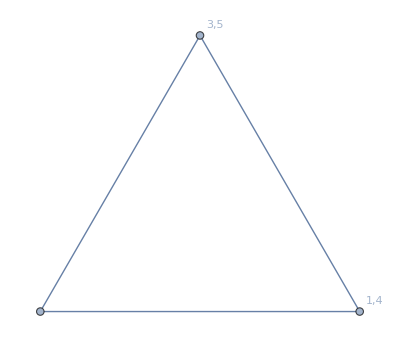

```mathematica
pic[104]
```

```mathematica
MyShow3[key_]:=Block[
{matrix=sols[key]/.{α2->δ1,β2->ϵ1,γ2->α1,δ2->β1,ϵ2->γ1}/.α+β+γ+δ+ϵ-λ->α1+β1+γ1+δ1+ϵ1},
Labeled[TableForm[Map[Map[TraditionalForm[#]&,#]&,matrix] ,TableAlignments->Center,TableHeadings->{ {1<->3,1<->4,2<->4,2<->5,3<->5,3<->7,4<->7},None}, TableDirections->Column],Style[TraditionalForm[FullSimplify[matrix[[1,1]]+matrix[[1,2]]]],Red,Bold]]
]
```

```mathematica
TableForm[Table[
Framed[Row[{Style[key,Darker[Green],Bold],If[KeyExistsQ[pic,key],Graph[pic[key],GraphLayout->"TutteEmbedding",VertexLabels->"Name", ImageSize->80, VertexLabelStyle->Darker[Darker[Green]]],Null],MyShow3[key]},"   "]],{key,Keys[sols]}]]
```

1-Graphics-1<->3 | α | λ-α
1<->4 | β | λ-β
2<->4 | γ | λ-γ
2<->5 | δ | λ-δ
3<->5 | ϵ | λ-ϵ
3<->7 | ζ | λ-ζ
4<->7 | η | λ-ηλ
      2-Graphics-1<->3 | α | 0
1<->4 | 0 | α
2<->4 | α1 | α-α1
2<->5 | δ1 | α-δ1
3<->5 | 0 | α
3<->7 | ζ1 | α-ζ1
4<->7 | η1 | α-η1α
      3-Graphics-1<->3 | 0 | λ-α
1<->4 | β | -α-β+λ
2<->4 | γ-α1 | -α+α1-γ+λ
2<->5 | δ-δ1 | -α-δ+δ1+λ
3<->5 | ϵ | -α+λ-ϵ
3<->7 | ζ-ζ1 | -α-ζ+ζ1+λ
4<->7 | η-η1 | -α-η+η1+λλ-α
      4-Graphics-1<->3 | 0 | β
1<->4 | β | 0
2<->4 | 0 | β
2<->5 | β1 | β-β1
3<->5 | ϵ1 | β-ϵ1
3<->7 | ζ2 | β-ζ2
4<->7 | η2 | β-η2β
      5-Graphics-1<->3 | α | -α-β+λ
1<->4 | 0 | λ-β
2<->4 | γ | -β-γ+λ
2<->5 | δ-β1 | -β+β1-δ+λ
3<->5 | ϵ-ϵ1 | -β+λ-ϵ+ϵ1
3<->7 | ζ-ζ2 | -β-ζ+ζ2+λ
4<->7 | η-η2 | -β-η+η2+λλ-β
      6-Graphics-1<->3 | α1 | γ-α1
1<->4 | 0 | γ
2<->4 | γ | 0
2<->5 | 0 | γ
3<->5 | γ1 | γ-γ1
3<->7 | ζ3 | γ-ζ3
4<->7 | η3 | γ-η3γ
      7-Graphics-1<->3 | α-α1 | -α+α1-γ+λ
1<->4 | β | -β-γ+λ
2<->4 | 0 | λ-γ
2<->5 | δ | -γ-δ+λ
3<->5 | ϵ-γ1 | -γ+γ1+λ-ϵ
3<->7 | ζ-ζ3 | -γ-ζ+ζ3+λ
4<->7 | η-η3 | -γ-η+η3+λλ-γ
      8-Graphics-1<->3 | δ1 | δ-δ1
1<->4 | β1 | δ-β1
2<->4 | 0 | δ
2<->5 | δ | 0
3<->5 | 0 | δ
3<->7 | ζ4 | δ-ζ4
4<->7 | η4 | δ-η4δ
      9-Graphics-1<->3 | α-δ1 | -α-δ+δ1+λ
1<->4 | β-β1 | -β+β1-δ+λ
2<->4 | γ | -γ-δ+λ
2<->5 | 0 | λ-δ
3<->5 | ϵ | -δ+λ-ϵ
3<->7 | ζ-ζ4 | -δ-ζ+ζ4+λ
4<->7 | η-η4 | -δ-η+η4+λλ-δ
      10-Graphics-1<->3 | 0 | ϵ
1<->4 | ϵ1 | ϵ-ϵ1
2<->4 | γ1 | ϵ-γ1
2<->5 | 0 | ϵ
3<->5 | ϵ | 0
3<->7 | ζ5 | ϵ-ζ5
4<->7 | η5 | ϵ-η5ϵ
      11-Graphics-1<->3 | α | -α+λ-ϵ
1<->4 | β-ϵ1 | -β+λ-ϵ+ϵ1
2<->4 | γ-γ1 | -γ+γ1+λ-ϵ
2<->5 | δ | -δ+λ-ϵ
3<->5 | 0 | λ-ϵ
3<->7 | ζ-ζ5 | -ζ+ζ5+λ-ϵ
4<->7 | η-η5 | -η+η5+λ-ϵλ-ϵ
      12-Graphics-1<->3 | 0 | -α-β+λ
1<->4 | 0 | -α-β+λ
2<->4 | γ-α1 | -α+α1-β-γ+λ
2<->5 | -β1+δ-δ1 | -α-β+β1-δ+δ1+λ
3<->5 | ϵ-ϵ1 | -α-β+λ-ϵ+ϵ1
3<->7 | ζ-ζ1-ζ2 | -α-β-ζ+ζ1+ζ2+λ
4<->7 | η-η1-η2 | -α-β-η+η1+η2+λ-α-β+λ
      13-Graphics-1<->3 | α-α1-δ1 | -α+α1-γ-δ+δ1+λ
1<->4 | β-β1 | -β+β1-γ-δ+λ
2<->4 | 0 | -γ-δ+λ
2<->5 | 0 | -γ-δ+λ
3<->5 | ϵ-γ1 | -γ+γ1-δ+λ-ϵ
3<->7 | ζ-ζ3-ζ4 | -γ-δ-ζ+ζ3+ζ4+λ
4<->7 | η-η3-η4 | -γ-δ-η+η3+η4+λ-γ-δ+λ
      14-Graphics-1<->3 | 0 | -α+λ-ϵ
1<->4 | β-ϵ1 | -α-β+λ-ϵ+ϵ1
2<->4 | -α1+γ-γ1 | -α+α1-γ+γ1+λ-ϵ
2<->5 | δ-δ1 | -α-δ+δ1+λ-ϵ
3<->5 | 0 | -α+λ-ϵ
3<->7 | ζ-ζ1-ζ5 | -α-ζ+ζ1+ζ5+λ-ϵ
4<->7 | η-η1-η5 | -α-η+η1+η5+λ-ϵ-α+λ-ϵ
      15-Graphics-1<->3 | α-α1 | -α+α1-β-γ+λ
1<->4 | 0 | -β-γ+λ
2<->4 | 0 | -β-γ+λ
2<->5 | δ-β1 | -β+β1-γ-δ+λ
3<->5 | -γ1+ϵ-ϵ1 | -β-γ+γ1+λ-ϵ+ϵ1
3<->7 | ζ-ζ2-ζ3 | -β-γ-ζ+ζ2+ζ3+λ
4<->7 | η-η2-η3 | -β-γ-η+η2+η3+λ-β-γ+λ
      16-Graphics-1<->3 | α-δ1 | -α-δ+δ1+λ-ϵ
1<->4 | β-β1-ϵ1 | -β+β1-δ+λ-ϵ+ϵ1
2<->4 | γ-γ1 | -γ+γ1-δ+λ-ϵ
2<->5 | 0 | -δ+λ-ϵ
3<->5 | 0 | -δ+λ-ϵ
3<->7 | ζ-ζ4-ζ5 | -δ-ζ+ζ4+ζ5+λ-ϵ
4<->7 | η-η4-η5 | -δ-η+η4+η5+λ-ϵ-δ+λ-ϵ
      17-Graphics-1<->3 | α1+δ1 | β1+γ1+ϵ1
1<->4 | β1+ϵ1 | α1+γ1+δ1
2<->4 | α1+γ1 | β1+δ1+ϵ1
2<->5 | β1+δ1 | α1+γ1+ϵ1
3<->5 | γ1+ϵ1 | α1+β1+δ1
3<->7 | -ζ+ζ1+ζ2+ζ3+ζ4+ζ5 | α1+β1+γ1+δ1+ζ-ζ1-ζ2-ζ3-ζ4-ζ5+ϵ1
4<->7 | -η+η1+η2+η3+η4+η5 | α1+β1+γ1+δ1+η-η1-η2-η3-η4-η5+ϵ1α1+β1+γ1+δ1+ϵ1
      18-Graphics-1<->3 | α1+δ1 | -α1+γ+δ-δ1+ϵ
1<->4 | β1+ϵ1 | -β1+γ+δ+ϵ-ϵ1
2<->4 | γ+γ1 | -γ1+δ+ϵ
2<->5 | δ | γ+ϵ
3<->5 | γ1+ϵ | γ-γ1+δ
3<->7 | ζ3+ζ4+ζ5 | γ+δ-ζ3-ζ4-ζ5+ϵ
4<->7 | η3+η4+η5 | γ+δ-η3-η4-η5+ϵγ+δ+ϵ
      19-Graphics-1<->3 | α | β+ϵ
1<->4 | β+ϵ1 | α+ϵ-ϵ1
2<->4 | α1+γ1 | α-α1+β-γ1+ϵ
2<->5 | β1+δ1 | α+β-β1-δ1+ϵ
3<->5 | ϵ+ϵ1 | α+β-ϵ1
3<->7 | ζ1+ζ2+ζ5 | α+β-ζ1-ζ2-ζ5+ϵ
4<->7 | η1+η2+η5 | α+β-η1-η2-η5+ϵα+β+ϵ
      20-Graphics-1<->3 | α1+δ1 | -α1+β+γ+δ-δ1
1<->4 | β+β1 | -β1+γ+δ
2<->4 | γ | β+δ
2<->5 | β1+δ | β-β1+γ
3<->5 | γ1+ϵ1 | β+γ-γ1+δ-ϵ1
3<->7 | ζ2+ζ3+ζ4 | β+γ+δ-ζ2-ζ3-ζ4
4<->7 | η2+η3+η4 | β+γ+δ-η2-η3-η4β+γ+δ
      21-Graphics-1<->3 | α+δ1 | δ-δ1+ϵ
1<->4 | β1+ϵ1 | α-β1+δ+ϵ-ϵ1
2<->4 | α1+γ1 | α-α1-γ1+δ+ϵ
2<->5 | δ+δ1 | α-δ1+ϵ
3<->5 | ϵ | α+δ
3<->7 | ζ1+ζ4+ζ5 | α+δ-ζ1-ζ4-ζ5+ϵ
4<->7 | η1+η4+η5 | α+δ-η1-η4-η5+ϵα+δ+ϵ
      22-Graphics-1<->3 | α+α1 | -α1+β+γ
1<->4 | β | α+γ
2<->4 | α1+γ | α-α1+β
2<->5 | β1+δ1 | α+β-β1+γ-δ1
3<->5 | γ1+ϵ1 | α+β+γ-γ1-ϵ1
3<->7 | ζ1+ζ2+ζ3 | α+β+γ-ζ1-ζ2-ζ3
4<->7 | η1+η2+η3 | α+β+γ-η1-η2-η3α+β+γ
      23-Graphics-1<->3 | α | -α+λ+ϵ
1<->4 | β+ϵ1 | -β+λ+ϵ-ϵ1
2<->4 | γ+γ1 | -γ-γ1+λ+ϵ
2<->5 | δ | -δ+λ+ϵ
3<->5 | 2 ϵ | λ-ϵ
3<->7 | ζ+ζ5 | -ζ-ζ5+λ+ϵ
4<->7 | η+η5 | -η-η5+λ+ϵλ+ϵ
      24-Graphics-1<->3 | α | -α+β+λ
1<->4 | 2 β | λ-β
2<->4 | γ | β-γ+λ
2<->5 | β1+δ | β-β1-δ+λ
3<->5 | ϵ+ϵ1 | β+λ-ϵ-ϵ1
3<->7 | ζ+ζ2 | β-ζ-ζ2+λ
4<->7 | η+η2 | β-η-η2+λβ+λ
      25-Graphics-1<->3 | α+δ1 | -α+δ-δ1+λ
1<->4 | β+β1 | -β-β1+δ+λ
2<->4 | γ | -γ+δ+λ
2<->5 | 2 δ | λ-δ
3<->5 | ϵ | δ+λ-ϵ
3<->7 | ζ+ζ4 | δ-ζ-ζ4+λ
4<->7 | η+η4 | δ-η-η4+λδ+λ
      26-Graphics-1<->3 | 2 α | λ-α
1<->4 | β | α-β+λ
2<->4 | α1+γ | α-α1-γ+λ
2<->5 | δ+δ1 | α-δ-δ1+λ
3<->5 | ϵ | α+λ-ϵ
3<->7 | ζ+ζ1 | α-ζ-ζ1+λ
4<->7 | η+η1 | α-η-η1+λα+λ
      27-Graphics-1<->3 | α+α1 | -α-α1+γ+λ
1<->4 | β | -β+γ+λ
2<->4 | 2 γ | λ-γ
2<->5 | δ | γ-δ+λ
3<->5 | γ1+ϵ | γ-γ1+λ-ϵ
3<->7 | ζ+ζ3 | γ-ζ-ζ3+λ
4<->7 | η+η3 | γ-η-η3+λγ+λ
      281<->3 | 2 α | 2 λ-2 α
1<->4 | 2 β | 2 λ-2 β
2<->4 | 2 γ | 2 λ-2 γ
2<->5 | 2 δ | 2 λ-2 δ
3<->5 | 2 ϵ | 2 λ-2 ϵ
3<->7 | 2 ζ | 2 λ-2 ζ
4<->7 | 2 η | 2 λ-2 η2 λ
      291<->3 | 2 α | 2 λ-2 α
1<->4 | 2 β | 2 λ-2 β
2<->4 | 2 γ | 2 λ-2 γ
2<->5 | 2 δ | 2 λ-2 δ
3<->5 | 2 ϵ | 2 λ-2 ϵ
3<->7 | 2 ζ | 2 λ-2 ζ
4<->7 | 2 η | 2 λ-2 η2 λ
      301<->3 | 2 α | 2 λ-2 α
1<->4 | 2 β | 2 λ-2 β
2<->4 | 2 γ | 2 λ-2 γ
2<->5 | 2 δ | 2 λ-2 δ
3<->5 | 2 ϵ | 2 λ-2 ϵ
3<->7 | 2 ζ | 2 λ-2 ζ
4<->7 | 2 η | 2 λ-2 η2 λ
      311<->3 | 2 α | 2 λ-2 α
1<->4 | 2 β | 2 λ-2 β
2<->4 | 2 γ | 2 λ-2 γ
2<->5 | 2 δ | 2 λ-2 δ
3<->5 | 2 ϵ | 2 λ-2 ϵ
3<->7 | 2 ζ | 2 λ-2 ζ
4<->7 | 2 η | 2 λ-2 η2 λ
      321<->3 | 2 α | 2 λ-2 α
1<->4 | 2 β | 2 λ-2 β
2<->4 | 2 γ | 2 λ-2 γ
2<->5 | 2 δ | 2 λ-2 δ
3<->5 | 2 ϵ | 2 λ-2 ϵ
3<->7 | 2 ζ | 2 λ-2 ζ
4<->7 | 2 η | 2 λ-2 η2 λ
      331<->3 | 2 α | -2 α+2 λ+ϵ
1<->4 | 2 β+ϵ1 | -2 β+2 λ+ϵ-ϵ1
2<->4 | 2 γ+γ1 | -2 γ-γ1+2 λ+ϵ
2<->5 | 2 δ | -2 δ+2 λ+ϵ
3<->5 | 3 ϵ | 2 λ-2 ϵ
3<->7 | 2 ζ+ζ5 | -2 ζ-ζ5+2 λ+ϵ
4<->7 | 2 η+η5 | -2 η-η5+2 λ+ϵ2 λ+ϵ
      341<->3 | 2 α | -2 α+β+2 λ
1<->4 | 3 β | 2 λ-2 β
2<->4 | 2 γ | β-2 γ+2 λ
2<->5 | β1+2 δ | β-β1-2 δ+2 λ
3<->5 | 2 ϵ+ϵ1 | β+2 λ-2 ϵ-ϵ1
3<->7 | 2 ζ+ζ2 | β-2 ζ-ζ2+2 λ
4<->7 | 2 η+η2 | β-2 η-η2+2 λβ+2 λ
      351<->3 | 2 α+δ1 | -2 α+δ-δ1+2 λ
1<->4 | 2 β+β1 | -2 β-β1+δ+2 λ
2<->4 | 2 γ | -2 γ+δ+2 λ
2<->5 | 3 δ | 2 λ-2 δ
3<->5 | 2 ϵ | δ+2 λ-2 ϵ
3<->7 | 2 ζ+ζ4 | δ-2 ζ-ζ4+2 λ
4<->7 | 2 η+η4 | δ-2 η-η4+2 λδ+2 λ
      361<->3 | 3 α | 2 λ-2 α
1<->4 | 2 β | α-2 β+2 λ
2<->4 | α1+2 γ | α-α1-2 γ+2 λ
2<->5 | 2 δ+δ1 | α-2 δ-δ1+2 λ
3<->5 | 2 ϵ | α+2 λ-2 ϵ
3<->7 | 2 ζ+ζ1 | α-2 ζ-ζ1+2 λ
4<->7 | 2 η+η1 | α-2 η-η1+2 λα+2 λ
      371<->3 | 2 α+α1 | -2 α-α1+γ+2 λ
1<->4 | 2 β | -2 β+γ+2 λ
2<->4 | 3 γ | 2 λ-2 γ
2<->5 | 2 δ | γ-2 δ+2 λ
3<->5 | γ1+2 ϵ | γ-γ1+2 λ-2 ϵ
3<->7 | 2 ζ+ζ3 | γ-2 ζ-ζ3+2 λ
4<->7 | 2 η+η3 | γ-2 η-η3+2 λγ+2 λ
      381<->3 | 3 α | 3 λ-3 α
1<->4 | 3 β | 3 λ-3 β
2<->4 | 3 γ | 3 λ-3 γ
2<->5 | 3 δ | 3 λ-3 δ
3<->5 | 3 ϵ | 3 λ-3 ϵ
3<->7 | 3 ζ | 3 λ-3 ζ
4<->7 | 3 η | 3 λ-3 η3 λ
      391<->3 | 3 α | 3 λ-3 α
1<->4 | 3 β | 3 λ-3 β
2<->4 | 3 γ | 3 λ-3 γ
2<->5 | 3 δ | 3 λ-3 δ
3<->5 | 3 ϵ | 3 λ-3 ϵ
3<->7 | 3 ζ | 3 λ-3 ζ
4<->7 | 3 η | 3 λ-3 η3 λ
      401<->3 | 3 α | 3 λ-3 α
1<->4 | 3 β | 3 λ-3 β
2<->4 | 3 γ | 3 λ-3 γ
2<->5 | 3 δ | 3 λ-3 δ
3<->5 | 3 ϵ | 3 λ-3 ϵ
3<->7 | 3 ζ | 3 λ-3 ζ
4<->7 | 3 η | 3 λ-3 η3 λ
      411<->3 | 3 α | 3 λ-3 α
1<->4 | 3 β | 3 λ-3 β
2<->4 | 3 γ | 3 λ-3 γ
2<->5 | 3 δ | 3 λ-3 δ
3<->5 | 3 ϵ | 3 λ-3 ϵ
3<->7 | 3 ζ | 3 λ-3 ζ
4<->7 | 3 η | 3 λ-3 η3 λ
      421<->3 | 3 α | 3 λ-3 α
1<->4 | 3 β | 3 λ-3 β
2<->4 | 3 γ | 3 λ-3 γ
2<->5 | 3 δ | 3 λ-3 δ
3<->5 | 3 ϵ | 3 λ-3 ϵ
3<->7 | 3 ζ | 3 λ-3 ζ
4<->7 | 3 η | 3 λ-3 η3 λ
      43-Graphics-1<->3 | α1 | -α1+γ+ϵ
1<->4 | ϵ1 | γ+ϵ-ϵ1
2<->4 | γ+γ1 | ϵ-γ1
2<->5 | 0 | γ+ϵ
3<->5 | γ1+ϵ | γ-γ1
3<->7 | ζ3+ζ5 | γ-ζ3-ζ5+ϵ
4<->7 | η3+η5 | γ-η3-η5+ϵγ+ϵ
      44-Graphics-1<->3 | 0 | β+ϵ
1<->4 | β+ϵ1 | ϵ-ϵ1
2<->4 | γ1 | β-γ1+ϵ
2<->5 | β1 | β-β1+ϵ
3<->5 | ϵ+ϵ1 | β-ϵ1
3<->7 | ζ2+ζ5 | β-ζ2-ζ5+ϵ
4<->7 | η2+η5 | β-η2-η5+ϵβ+ϵ
      45-Graphics-1<->3 | δ1 | β+δ-δ1
1<->4 | β+β1 | δ-β1
2<->4 | 0 | β+δ
2<->5 | β1+δ | β-β1
3<->5 | ϵ1 | β+δ-ϵ1
3<->7 | ζ2+ζ4 | β+δ-ζ2-ζ4
4<->7 | η2+η4 | β+δ-η2-η4β+δ
      46-Graphics-1<->3 | α+δ1 | δ-δ1
1<->4 | β1 | α-β1+δ
2<->4 | α1 | α-α1+δ
2<->5 | δ+δ1 | α-δ1
3<->5 | 0 | α+δ
3<->7 | ζ1+ζ4 | α+δ-ζ1-ζ4
4<->7 | η1+η4 | α+δ-η1-η4α+δ
      47-Graphics-1<->3 | α+α1 | γ-α1
1<->4 | 0 | α+γ
2<->4 | α1+γ | α-α1
2<->5 | δ1 | α+γ-δ1
3<->5 | γ1 | α+γ-γ1
3<->7 | ζ1+ζ3 | α+γ-ζ1-ζ3
4<->7 | η1+η3 | α+γ-η1-η3α+γ
      481<->3 | 2 α | -α+β+λ
1<->4 | 2 β | α-β+λ
2<->4 | α1+γ | α-α1+β-γ+λ
2<->5 | β1+δ+δ1 | α+β-β1-δ-δ1+λ
3<->5 | ϵ+ϵ1 | α+β+λ-ϵ-ϵ1
3<->7 | ζ+ζ1+ζ2 | α+β-ζ-ζ1-ζ2+λ
4<->7 | η+η1+η2 | α+β-η-η1-η2+λα+β+λ
      491<->3 | α+α1+δ1 | -α-α1+γ+δ-δ1+λ
1<->4 | β+β1 | -β-β1+γ+δ+λ
2<->4 | 2 γ | -γ+δ+λ
2<->5 | 2 δ | γ-δ+λ
3<->5 | γ1+ϵ | γ-γ1+δ+λ-ϵ
3<->7 | ζ+ζ3+ζ4 | γ+δ-ζ-ζ3-ζ4+λ
4<->7 | η+η3+η4 | γ+δ-η-η3-η4+λγ+δ+λ
      50-Graphics-1<->3 | 4 (α1+δ1) | 4 (-α1+γ+δ-δ1+ϵ)
1<->4 | 4 (β1+ϵ1) | 4 (-β1+γ+δ+ϵ-ϵ1)
2<->4 | 4 (γ+γ1) | 4 (-γ1+δ+ϵ)
2<->5 | 4 δ | 4 (γ+ϵ)
3<->5 | 4 (γ1+ϵ) | 4 (γ-γ1+δ)
3<->7 | 4 (ζ3+ζ4+ζ5) | 4 (γ+δ-ζ3-ζ4-ζ5+ϵ)
4<->7 | 4 (η3+η4+η5) | 4 (γ+δ-η3-η4-η5+ϵ)4 (γ+δ+ϵ)
      51-Graphics-1<->3 | 3 (α1+δ1) | 3 (-α1+γ+δ-δ1+ϵ)
1<->4 | 3 (β1+ϵ1) | 3 (-β1+γ+δ+ϵ-ϵ1)
2<->4 | 3 (γ+γ1) | 3 (-γ1+δ+ϵ)
2<->5 | 3 δ | 3 (γ+ϵ)
3<->5 | 3 (γ1+ϵ) | 3 (γ-γ1+δ)
3<->7 | 3 (ζ3+ζ4+ζ5) | 3 (γ+δ-ζ3-ζ4-ζ5+ϵ)
4<->7 | 3 (η3+η4+η5) | 3 (γ+δ-η3-η4-η5+ϵ)3 (γ+δ+ϵ)
      52-Graphics-1<->3 | 2 (α1+δ1) | 2 (-α1+γ+δ-δ1+ϵ)
1<->4 | 2 (β1+ϵ1) | 2 (-β1+γ+δ+ϵ-ϵ1)
2<->4 | 2 (γ+γ1) | 2 (-γ1+δ+ϵ)
2<->5 | 2 δ | 2 (γ+ϵ)
3<->5 | 2 (γ1+ϵ) | 2 (γ-γ1+δ)
3<->7 | 2 (ζ3+ζ4+ζ5) | 2 (γ+δ-ζ3-ζ4-ζ5+ϵ)
4<->7 | 2 (η3+η4+η5) | 2 (γ+δ-η3-η4-η5+ϵ)2 (γ+δ+ϵ)
      53-Graphics-1<->3 | α1+δ1 | -α-α1-β+γ+δ-δ1+λ+ϵ
1<->4 | β1+ϵ1 | -α-β-β1+γ+δ+λ+ϵ-ϵ1
2<->4 | -α1+2 γ+γ1 | -α+α1-β-γ-γ1+δ+λ+ϵ
2<->5 | -β1+2 δ-δ1 | -α-β+β1+γ-δ+δ1+λ+ϵ
3<->5 | γ1+2 ϵ-ϵ1 | -α-β+γ-γ1+δ+λ-ϵ+ϵ1
3<->7 | ζ-ζ1-ζ2+ζ3+ζ4+ζ5 | -α-β+γ+δ-ζ+ζ1+ζ2-ζ3-ζ4-ζ5+λ+ϵ
4<->7 | η-η1-η2+η3+η4+η5 | -α-β+γ+δ-η+η1+η2-η3-η4-η5+λ+ϵ-α-β+γ+δ+λ+ϵ
      54-Graphics-1<->3 | δ1 | -α-β+δ-δ1+λ
1<->4 | β1 | -α-β-β1+δ+λ
2<->4 | γ-α1 | -α+α1-β-γ+δ+λ
2<->5 | -β1+2 δ-δ1 | -α-β+β1-δ+δ1+λ
3<->5 | ϵ-ϵ1 | -α-β+δ+λ-ϵ+ϵ1
3<->7 | ζ-ζ1-ζ2+ζ4 | -α-β+δ-ζ+ζ1+ζ2-ζ4+λ
4<->7 | η-η1-η2+η4 | -α-β+δ-η+η1+η2-η4+λ-α-β+δ+λ
      551<->3 | 4 α | 4 (β+ϵ)
1<->4 | 4 (β+ϵ1) | 4 (α+ϵ-ϵ1)
2<->4 | 4 (α1+γ1) | 4 (α-α1+β-γ1+ϵ)
2<->5 | 4 (β1+δ1) | 4 (α+β-β1-δ1+ϵ)
3<->5 | 4 (ϵ+ϵ1) | 4 (α+β-ϵ1)
3<->7 | 4 (ζ1+ζ2+ζ5) | 4 (α+β-ζ1-ζ2-ζ5+ϵ)
4<->7 | 4 (η1+η2+η5) | 4 (α+β-η1-η2-η5+ϵ)4 (α+β+ϵ)
      561<->3 | 3 α | 3 (β+ϵ)
1<->4 | 3 (β+ϵ1) | 3 (α+ϵ-ϵ1)
2<->4 | 3 (α1+γ1) | 3 (α-α1+β-γ1+ϵ)
2<->5 | 3 (β1+δ1) | 3 (α+β-β1-δ1+ϵ)
3<->5 | 3 (ϵ+ϵ1) | 3 (α+β-ϵ1)
3<->7 | 3 (ζ1+ζ2+ζ5) | 3 (α+β-ζ1-ζ2-ζ5+ϵ)
4<->7 | 3 (η1+η2+η5) | 3 (α+β-η1-η2-η5+ϵ)3 (α+β+ϵ)
      571<->3 | 2 α | 2 (β+ϵ)
1<->4 | 2 (β+ϵ1) | 2 (α+ϵ-ϵ1)
2<->4 | 2 (α1+γ1) | 2 (α-α1+β-γ1+ϵ)
2<->5 | 2 (β1+δ1) | 2 (α+β-β1-δ1+ϵ)
3<->5 | 2 (ϵ+ϵ1) | 2 (α+β-ϵ1)
3<->7 | 2 (ζ1+ζ2+ζ5) | 2 (α+β-ζ1-ζ2-ζ5+ϵ)
4<->7 | 2 (η1+η2+η5) | 2 (α+β-η1-η2-η5+ϵ)2 (α+β+ϵ)
      581<->3 | 2 α-α1-δ1 | -α+α1+β-γ-δ+δ1+λ+ϵ
1<->4 | 2 β-β1+ϵ1 | α-β+β1-γ-δ+λ+ϵ-ϵ1
2<->4 | α1+γ1 | α-α1+β-γ-γ1-δ+λ+ϵ
2<->5 | β1+δ1 | α+β-β1-γ-δ-δ1+λ+ϵ
3<->5 | -γ1+2 ϵ+ϵ1 | α+β-γ+γ1-δ+λ-ϵ-ϵ1
3<->7 | ζ+ζ1+ζ2-ζ3-ζ4+ζ5 | α+β-γ-δ-ζ-ζ1-ζ2+ζ3+ζ4-ζ5+λ+ϵ
4<->7 | η+η1+η2-η3-η4+η5 | α+β-γ-δ-η-η1-η2+η3+η4-η5+λ+ϵα+β-γ-δ+λ+ϵ
      591<->3 | 2 α-α1-δ1 | -α+α1-γ-δ+δ1+λ
1<->4 | β-β1 | α-β+β1-γ-δ+λ
2<->4 | α1 | α-α1-γ-δ+λ
2<->5 | δ1 | α-γ-δ-δ1+λ
3<->5 | ϵ-γ1 | α-γ+γ1-δ+λ-ϵ
3<->7 | ζ+ζ1-ζ3-ζ4 | α-γ-δ-ζ-ζ1+ζ3+ζ4+λ
4<->7 | η+η1-η3-η4 | α-γ-δ-η-η1+η3+η4+λα-γ-δ+λ
      601<->3 | 4 (α1+δ1) | 4 (-α1+β+γ+δ-δ1)
1<->4 | 4 (β+β1) | 4 (-β1+γ+δ)
2<->4 | 4 γ | 4 (β+δ)
2<->5 | 4 (β1+δ) | 4 (β-β1+γ)
3<->5 | 4 (γ1+ϵ1) | 4 (β+γ-γ1+δ-ϵ1)
3<->7 | 4 (ζ2+ζ3+ζ4) | 4 (β+γ+δ-ζ2-ζ3-ζ4)
4<->7 | 4 (η2+η3+η4) | 4 (β+γ+δ-η2-η3-η4)4 (β+γ+δ)
      611<->3 | 3 (α1+δ1) | 3 (-α1+β+γ+δ-δ1)
1<->4 | 3 (β+β1) | 3 (-β1+γ+δ)
2<->4 | 3 γ | 3 (β+δ)
2<->5 | 3 (β1+δ) | 3 (β-β1+γ)
3<->5 | 3 (γ1+ϵ1) | 3 (β+γ-γ1+δ-ϵ1)
3<->7 | 3 (ζ2+ζ3+ζ4) | 3 (β+γ+δ-ζ2-ζ3-ζ4)
4<->7 | 3 (η2+η3+η4) | 3 (β+γ+δ-η2-η3-η4)3 (β+γ+δ)
      621<->3 | 2 (α1+δ1) | 2 (-α1+β+γ+δ-δ1)
1<->4 | 2 (β+β1) | 2 (-β1+γ+δ)
2<->4 | 2 γ | 2 (β+δ)
2<->5 | 2 (β1+δ) | 2 (β-β1+γ)
3<->5 | 2 (γ1+ϵ1) | 2 (β+γ-γ1+δ-ϵ1)
3<->7 | 2 (ζ2+ζ3+ζ4) | 2 (β+γ+δ-ζ2-ζ3-ζ4)
4<->7 | 2 (η2+η3+η4) | 2 (β+γ+δ-η2-η3-η4)2 (β+γ+δ)
      631<->3 | α1+δ1 | -α-α1+β+γ+δ-δ1+λ-ϵ
1<->4 | 2 β+β1-ϵ1 | -α-β-β1+γ+δ+λ-ϵ+ϵ1
2<->4 | -α1+2 γ-γ1 | -α+α1+β-γ+γ1+δ+λ-ϵ
2<->5 | β1+2 δ-δ1 | -α+β-β1+γ-δ+δ1+λ-ϵ
3<->5 | γ1+ϵ1 | -α+β+γ-γ1+δ+λ-ϵ-ϵ1
3<->7 | ζ-ζ1+ζ2+ζ3+ζ4-ζ5 | -α+β+γ+δ-ζ+ζ1-ζ2-ζ3-ζ4+ζ5+λ-ϵ
4<->7 | η-η1+η2+η3+η4-η5 | -α+β+γ+δ-η+η1-η2-η3-η4+η5+λ-ϵ-α+β+γ+δ+λ-ϵ
      641<->3 | α1 | -α-α1+γ+λ-ϵ
1<->4 | β-ϵ1 | -α-β+γ+λ-ϵ+ϵ1
2<->4 | -α1+2 γ-γ1 | -α+α1-γ+γ1+λ-ϵ
2<->5 | δ-δ1 | -α+γ-δ+δ1+λ-ϵ
3<->5 | γ1 | -α+γ-γ1+λ-ϵ
3<->7 | ζ-ζ1+ζ3-ζ5 | -α+γ-ζ+ζ1-ζ3+ζ5+λ-ϵ
4<->7 | η-η1+η3-η5 | -α+γ-η+η1-η3+η5+λ-ϵ-α+γ+λ-ϵ
      651<->3 | 4 (α+δ1) | 4 (δ-δ1+ϵ)
1<->4 | 4 (β1+ϵ1) | 4 (α-β1+δ+ϵ-ϵ1)
2<->4 | 4 (α1+γ1) | 4 (α-α1-γ1+δ+ϵ)
2<->5 | 4 (δ+δ1) | 4 (α-δ1+ϵ)
3<->5 | 4 ϵ | 4 (α+δ)
3<->7 | 4 (ζ1+ζ4+ζ5) | 4 (α+δ-ζ1-ζ4-ζ5+ϵ)
4<->7 | 4 (η1+η4+η5) | 4 (α+δ-η1-η4-η5+ϵ)4 (α+δ+ϵ)
      661<->3 | 3 (α+δ1) | 3 (δ-δ1+ϵ)
1<->4 | 3 (β1+ϵ1) | 3 (α-β1+δ+ϵ-ϵ1)
2<->4 | 3 (α1+γ1) | 3 (α-α1-γ1+δ+ϵ)
2<->5 | 3 (δ+δ1) | 3 (α-δ1+ϵ)
3<->5 | 3 ϵ | 3 (α+δ)
3<->7 | 3 (ζ1+ζ4+ζ5) | 3 (α+δ-ζ1-ζ4-ζ5+ϵ)
4<->7 | 3 (η1+η4+η5) | 3 (α+δ-η1-η4-η5+ϵ)3 (α+δ+ϵ)
      671<->3 | 2 (α+δ1) | 2 (δ-δ1+ϵ)
1<->4 | 2 (β1+ϵ1) | 2 (α-β1+δ+ϵ-ϵ1)
2<->4 | 2 (α1+γ1) | 2 (α-α1-γ1+δ+ϵ)
2<->5 | 2 (δ+δ1) | 2 (α-δ1+ϵ)
3<->5 | 2 ϵ | 2 (α+δ)
3<->7 | 2 (ζ1+ζ4+ζ5) | 2 (α+δ-ζ1-ζ4-ζ5+ϵ)
4<->7 | 2 (η1+η4+η5) | 2 (α+δ-η1-η4-η5+ϵ)2 (α+δ+ϵ)
      681<->3 | 2 α-α1+δ1 | -α+α1-β-γ+δ-δ1+λ+ϵ
1<->4 | β1+ϵ1 | α-β-β1-γ+δ+λ+ϵ-ϵ1
2<->4 | α1+γ1 | α-α1-β-γ-γ1+δ+λ+ϵ
2<->5 | -β1+2 δ+δ1 | α-β+β1-γ-δ-δ1+λ+ϵ
3<->5 | -γ1+2 ϵ-ϵ1 | α-β-γ+γ1+δ+λ-ϵ+ϵ1
3<->7 | ζ+ζ1-ζ2-ζ3+ζ4+ζ5 | α-β-γ+δ-ζ-ζ1+ζ2+ζ3-ζ4-ζ5+λ+ϵ
4<->7 | η+η1-η2-η3+η4+η5 | α-β-γ+δ-η-η1+η2+η3-η4-η5+λ+ϵα-β-γ+δ+λ+ϵ
      691<->3 | α-α1 | -α+α1-β-γ+λ+ϵ
1<->4 | ϵ1 | -β-γ+λ+ϵ-ϵ1
2<->4 | γ1 | -β-γ-γ1+λ+ϵ
2<->5 | δ-β1 | -β+β1-γ-δ+λ+ϵ
3<->5 | -γ1+2 ϵ-ϵ1 | -β-γ+γ1+λ-ϵ+ϵ1
3<->7 | ζ-ζ2-ζ3+ζ5 | -β-γ-ζ+ζ2+ζ3-ζ5+λ+ϵ
4<->7 | η-η2-η3+η5 | -β-γ-η+η2+η3-η5+λ+ϵ-β-γ+λ+ϵ
      701<->3 | 4 (α+α1) | 4 (-α1+β+γ)
1<->4 | 4 β | 4 (α+γ)
2<->4 | 4 (α1+γ) | 4 (α-α1+β)
2<->5 | 4 (β1+δ1) | 4 (α+β-β1+γ-δ1)
3<->5 | 4 (γ1+ϵ1) | 4 (α+β+γ-γ1-ϵ1)
3<->7 | 4 (ζ1+ζ2+ζ3) | 4 (α+β+γ-ζ1-ζ2-ζ3)
4<->7 | 4 (η1+η2+η3) | 4 (α+β+γ-η1-η2-η3)4 (α+β+γ)
      711<->3 | 3 (α+α1) | 3 (-α1+β+γ)
1<->4 | 3 β | 3 (α+γ)
2<->4 | 3 (α1+γ) | 3 (α-α1+β)
2<->5 | 3 (β1+δ1) | 3 (α+β-β1+γ-δ1)
3<->5 | 3 (γ1+ϵ1) | 3 (α+β+γ-γ1-ϵ1)
3<->7 | 3 (ζ1+ζ2+ζ3) | 3 (α+β+γ-ζ1-ζ2-ζ3)
4<->7 | 3 (η1+η2+η3) | 3 (α+β+γ-η1-η2-η3)3 (α+β+γ)
      721<->3 | 2 (α+α1) | 2 (-α1+β+γ)
1<->4 | 2 β | 2 (α+γ)
2<->4 | 2 (α1+γ) | 2 (α-α1+β)
2<->5 | 2 (β1+δ1) | 2 (α+β-β1+γ-δ1)
3<->5 | 2 (γ1+ϵ1) | 2 (α+β+γ-γ1-ϵ1)
3<->7 | 2 (ζ1+ζ2+ζ3) | 2 (α+β+γ-ζ1-ζ2-ζ3)
4<->7 | 2 (η1+η2+η3) | 2 (α+β+γ-η1-η2-η3)2 (α+β+γ)
      731<->3 | 2 α+α1-δ1 | -α-α1+β+γ-δ+δ1+λ-ϵ
1<->4 | 2 β-β1-ϵ1 | α-β+β1+γ-δ+λ-ϵ+ϵ1
2<->4 | α1+2 γ-γ1 | α-α1+β-γ+γ1-δ+λ-ϵ
2<->5 | β1+δ1 | α+β-β1+γ-δ-δ1+λ-ϵ
3<->5 | γ1+ϵ1 | α+β+γ-γ1-δ+λ-ϵ-ϵ1
3<->7 | ζ+ζ1+ζ2+ζ3-ζ4-ζ5 | α+β+γ-δ-ζ-ζ1-ζ2-ζ3+ζ4+ζ5+λ-ϵ
4<->7 | η+η1+η2+η3-η4-η5 | α+β+γ-δ-η-η1-η2-η3+η4+η5+λ-ϵα+β+γ-δ+λ-ϵ
      741<->3 | α-δ1 | -α+β-δ+δ1+λ-ϵ
1<->4 | 2 β-β1-ϵ1 | -β+β1-δ+λ-ϵ+ϵ1
2<->4 | γ-γ1 | β-γ+γ1-δ+λ-ϵ
2<->5 | β1 | β-β1-δ+λ-ϵ
3<->5 | ϵ1 | β-δ+λ-ϵ-ϵ1
3<->7 | ζ+ζ2-ζ4-ζ5 | β-δ-ζ-ζ2+ζ4+ζ5+λ-ϵ
4<->7 | η+η2-η4-η5 | β-δ-η-η2+η4+η5+λ-ϵβ-δ+λ-ϵ
      100-Graphics-1<->3 | α1 | 0
1<->4 | 0 | α1
2<->4 | α1 | 0
2<->5 | 0 | α1
3<->5 | 0 | α1
3<->7 | ζ6 | α1-ζ6
4<->7 | η6 | α1-η6α1
      101-Graphics-1<->3 | 0 | β1
1<->4 | β1 | 0
2<->4 | 0 | β1
2<->5 | 0 | β1
3<->5 | β1 | 0
3<->7 | ζ7 | β1-ζ7
4<->7 | η7 | β1-η7β1
      102-Graphics-1<->3 | 0 | γ1
1<->4 | 0 | γ1
2<->4 | 0 | γ1
2<->5 | γ1 | 0
3<->5 | γ1 | 0
3<->7 | ζ8 | γ1-ζ8
4<->7 | η8 | γ1-η8γ1
      103-Graphics-1<->3 | δ1 | 0
1<->4 | 0 | δ1
2<->4 | 0 | δ1
2<->5 | δ1 | 0
3<->5 | 0 | δ1
3<->7 | ζ7 | δ1-ζ7
4<->7 | η7 | δ1-η7δ1
      104-Graphics-1<->3 | 0 | ϵ1
1<->4 | ϵ1 | 0
2<->4 | 0 | ϵ1
2<->5 | 0 | ϵ1
3<->5 | ϵ1 | 0
3<->7 | ζ10 | ϵ1-ζ10
4<->7 | η10 | ϵ1-η10ϵ1

```mathematica
Table[op[key]=Greater;1,{key,Keys[sols]}];op[17]=GreaterEqual
```

GreaterEqual

```mathematica
ExpressionToTable[exp_]:=Table[exp[[i]],{i,1,Length[exp]}]//Sort//TableForm
```

```mathematica
Fold[And,Map[FullSimplify[#]&,DeleteDuplicates[Flatten[Table[Table[{op[key][sols[key][[k,1]]+sols[key][[k,2]],0],sols[key][[k,1]]>=0,sols[key][[k,2]]≥0},{k,1,7}],{key,Keys[sols]}]]]/.{α2->δ1,β2->ϵ1,γ2->α1,δ2->β1,ϵ2->γ1}/.λ->(α+β+γ+δ+ϵ-(α1+β1+γ1+δ1+ϵ1))//Sort
]//DeleteDuplicates//Sort]//FullSimplify//ExpressionToTable
```

$Aborted

```mathematica
{{ζ-ζ1-ζ2+ζ4}, {η-η1-η2+η4}}
```

```mathematica
Fold[And,Map[FullSimplify[#]&,DeleteDuplicates[Flatten[Table[Table[{op[key][sols[key][[k,1]]+sols[key][[k,2]],0],sols[key][[k,1]]>=0,sols[key][[k,2]]≥0},{k,1,7}],{key,Keys[sols]}]]]/.{α2->δ1,β2->ϵ1,γ2->α1,δ2->β1,ϵ2->γ1}/.λ->(α+β+γ+δ+ϵ-(α1+β1+γ1+δ1+ϵ1))//Sort
]//DeleteDuplicates//Sort]&&γ-γ1>0&&ϵ-ϵ1>0&& η1>0&&η2>0&&η3>0&&η4>0&&η5>0&&ζ1>0&&ζ2>0&&ζ3>0&&ζ4>0&&ζ5>0//FullSimplify//ExpressionToTable
```

ζ1>0
ζ2>0
ζ3>0
ζ4>0
ζ5>0
η1>0
η2>0
η3>0
η4>0
η5>0
α1≥0
β1≥0
γ1≥0
δ1≥0
ϵ1≥0
γ1<γ
ϵ1<ϵ
α1+β1+γ1+δ1+ϵ1<β+γ+δ
α1+β1+γ1+δ1+ϵ1<α+β+ϵ
α1+β1+γ1+δ1+ϵ1<α+δ+ϵ
α1+γ1≤γ
α1+δ1≤α
β1+δ1≤δ
β1+ϵ1≤β
γ1+ϵ1≤ϵ
ζ≤ζ1+ζ2+ζ3+ζ4+ζ5
α1+β1+γ1+δ1+ϵ1+ζ≤γ+δ+ϵ+ζ1+ζ2
α1+β1+γ1+δ1+ϵ1+ζ≤α+δ+ϵ+ζ2+ζ3
α1+β1+γ1+δ1+ϵ1+ζ≤α+β+ϵ+ζ3+ζ4
α1+β1+γ1+δ1+ϵ1+ζ≤β+γ+δ+ζ1+ζ5
α1+β1+γ1+δ1+ϵ1+ζ≤α+β+γ+ζ4+ζ5
ζ1≤α
ζ2≤β
ζ1+ζ2≤ζ
ζ3≤γ
ζ2+ζ3≤ζ
ζ4≤δ
ζ3+ζ4≤ζ
ζ5≤ϵ
ζ1+ζ5≤ζ
ζ4+ζ5≤ζ
ζ1+ζ2+ζ3+ζ4+ζ5≤α1+β1+γ1+δ1+ϵ1+ζ
η≤η1+η2+η3+η4+η5
α1+β1+γ1+δ1+ϵ1+η≤γ+δ+ϵ+η1+η2
α1+β1+γ1+δ1+ϵ1+η≤α+δ+ϵ+η2+η3
α1+β1+γ1+δ1+ϵ1+η≤α+β+ϵ+η3+η4
α1+β1+γ1+δ1+ϵ1+η≤β+γ+δ+η1+η5
α1+β1+γ1+δ1+ϵ1+η≤α+β+γ+η4+η5
η1≤α
η2≤β
η1+η2≤η
η3≤γ
η2+η3≤η
η4≤δ
η3+η4≤η
η5≤ϵ
η1+η5≤η
η4+η5≤η
η1+η2+η3+η4+η5≤α1+β1+γ1+δ1+ϵ1+η

```mathematica
Fold[And,Map[FullSimplify[#]&,DeleteDuplicates[Flatten[Table[Table[{op[key][sols[key][[k,1]]+sols[key][[k,2]],0],sols[key][[k,1]]>=0,sols[key][[k,2]]≥0},{k,1,5}]/.{α2->δ1,β2->ϵ1,γ2->α1,δ2->β1,ϵ2->γ1},{key,Keys[sols]}]]]//Sort
]//DeleteDuplicates//Sort]//FullSimplify//ExpressionToTable
```

α>0
β>0
γ>0
δ>0
ϵ>0
α1≥0
β1≥0
γ1≥0
δ1≥0
ϵ1≥0
α+β<λ
β+γ<λ
γ+δ<λ
α+ϵ<λ
δ+ϵ<λ
α+β+γ≤α1+λ
α1+γ1≤γ
α+β+δ≤β1+δ1+λ
α+γ+δ≤α1+δ1+λ
β+γ+δ≤β1+λ
α1+δ1≤α
β1+δ1≤δ
α+β+ϵ≤ϵ1+λ
α+γ+ϵ≤α1+γ1+λ
β+γ+ϵ≤γ1+ϵ1+λ
α+δ+ϵ≤δ1+λ
β+δ+ϵ≤β1+ϵ1+λ
γ+δ+ϵ≤γ1+λ
β1+ϵ1≤β
γ1+ϵ1≤ϵ
α1+γ1+λ≤α+β+γ+δ+ϵ
α1+δ1+λ≤α+β+γ+δ+ϵ
β1+δ1+λ≤α+β+γ+δ+ϵ
β1+ϵ1+λ≤α+β+γ+δ+ϵ
γ1+ϵ1+λ≤α+β+γ+δ+ϵ